# 5. GRAFOS: REPRESENTACIÓN E IMPLEMETACIÓN

*Las entradas de cada ejemplo deben ser ejecutados en orden para su correcto funcionamiento.

1. DEFINICIÓN Y TIPOS DE GRAFOS

#### Ejemplo 5.1.

```mathematica
W1={1,2,3};
F1={2->1,1->3,3->2};
```

```mathematica
W2={1,2,3,4,5};
F2={1->2,2->3,3->4};
```

```mathematica
<<Combinatorica`
```

```mathematica
G1=Graph[{{{2,1}},{{3,2}},{{1,3}}},{{{0,1}},{{1,0}},{{-1,0}}},EdgeDirection->True]
```

⁃Graph:<3,3,Directed>⁃

```mathematica
G2=Graph[{{{1,2}},{{2,3}},{{3,4}}},{{{0,2}},{{1,1}},{{0,1}},{{1,0}},{{1,2}}}]
```

⁃Graph:<3,5,Undirected>⁃

```mathematica
Edges[G1]
```

{{2,1},{3,2},{1,3}}

```mathematica
Vertices[G1]
```

{{0,1},{1,0},{-1,0}}

```mathematica
M[G1]
```

3

```mathematica
V[G1]
```

3

```mathematica
Edges[G2]
```

{{1,2},{2,3},{3,4}}

```mathematica
Vertices[G2]
```

{{0,2},{1,1},{0,1},{1,0},{1,2}}

```mathematica
M[G2]
```

3

```mathematica
V[G2]
```

5

## 2. REPRESENTACIÓN MATRICIAL

### 2.2. Matriz de adyacencia

#### Función 5.1. MATRIZADYACENCIA[]

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

#### Función 5.2. MATRIZADYACENCIADIR[]

```mathematica
MATRIZADYACENCIADIR[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1,{k,Length[F]}];
matrizadyacencia];
```

#### Función 5.1.bis. MATRIZADYACENCIA[]

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{i,sparsematriz,CONTADORi,nuevoF},   
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
sparsematriz=SparseArray[Table[{nuevoF[[i]][[1]],nuevoF[[i]][[2]]}->1,{i,Length[F]}] ,{Length[W],Length[W]}];
matrizadyacencia=sparsematriz+Transpose[sparsematriz];
Normal[matrizadyacencia]
];
```

#### Función 5.2.bis. MATRIZADYACENCIADIR[]

```mathematica
MATRIZADYACENCIADIR[W_,F_]:=Module[{i,CONTADORi,nuevoF},         
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=SparseArray[Table[{nuevoF[[i]][[1]],nuevoF[[i]][[2]]}->1,{i,Length[F]}],{Length[W],Length[W]}];
Normal[matrizadyacencia]
];
```

#### Programa 5.3. Cálculo de los vértices y lados de un grafo no orientado desde la matriz de adyacencia

matrizadyacencia=MATRIZ DE ADYACENCIA;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i→j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F

#### Programa 5.4. Cálculo de los vértices y lados de un grafo dirigido desde la matriz de adyacencia

matrizadyacencia=MATRIZ DE ADYACENCIA;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i→j]];
        ,{i,Dimensions[matrizadyacencia][[1]]}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F

#### Observación:

```mathematica
antiguoF=Table[antiguoW[[F[[i]][[1]]]]-> antiguoW[[F[[i]][[2]]]],{i,Length[F]}]
```

#### Ejemplo 5.2.

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{i,sparsematriz,CONTADORi,nuevoF},   
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
sparsematriz=SparseArray[Table[{nuevoF[[i]][[1]],nuevoF[[i]][[2]]}->1,{i,Length[F]}] ,{Length[W],Length[W]}];
matrizadyacencia=sparsematriz+Transpose[sparsematriz];
Normal[matrizadyacencia]
];
```

```mathematica
MATRIZADYACENCIADIR[W_,F_]:=Module[{i,CONTADORi,nuevoF},         
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=SparseArray[Table[{nuevoF[[i]][[1]],nuevoF[[i]][[2]]}->1,{i,Length[F]}],{Length[W],Length[W]}];
Normal[matrizadyacencia]
];
```

Matriz de adyacencia de G_1:

```mathematica
W1={1,2,3};
F1={2->1,1->3,3->2};
```

```mathematica
A=MATRIZADYACENCIADIR[W1,F1];
MatrixForm[A]
```

(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0)

Matriz de adyacencia de G_2:

```mathematica
W2={1,2,3,4,5};
F2={1->2,2->3,3->4};
```

```mathematica
B=MATRIZADYACENCIA[W2,F2];
MatrixForm[B]
```

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

Recuperamos el conjunto de vértices y el de flechas de G_1:

```mathematica
matrizadyacencia=A;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1,2,3}

{2→1,3→2,1→3}

Recuperamos el conjunto de vértices y el de lados de G_2:

```mathematica
matrizadyacencia=B;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1,2,3,4,5}

{1→2,2→3,3→4}

Matriz de adyacencia de G_3:

```mathematica
W={a,b,c,d,e};
F={a->b,b->c,c->d,d->e,e->a};
```

```mathematica
matriz=MATRIZADYACENCIA[W,F]
```

{{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}}

Recuperamos el conjunto de vértices y el de lados de G_3:

```mathematica
matrizadyacencia=matriz;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1,2,3,4,5}

{1→2,2→3,3→4,1→5,4→5}

Recuperamos la información perdida relativa a los nombres de los vértices de G_3:

```mathematica
antiguoW={a,b,c,d,e}
antiguoF=Table[antiguoW[[F[[i]][[1]]]]-> antiguoW[[F[[i]][[2]]]],{i,Length[F]}]
```

{a,b,c,d,e}

{a→b,b→c,c→d,a→e,d→e}

Ahora loa hacemos con AjacencyMatrix[], para ilustrar su funcionamiento la aplicamos G_3, pero introducimos el conjunto de lados de dos formas disntas, cambiando el orden de los lados:

```mathematica
W={a,b,c,d,e};
F1={a->b,e->a,b->c,c->d,d->e};
F2={d->e,b->c,a->b,c->d,e->a};
F={a->b,b->c,c->d,d->e,e->a};
```

```mathematica
<<"GraphUtilities`";
```

```mathematica
matriz1=AdjacencyMatrix[F];
matriz1=matriz1+Transpose[matriz1]
```

SparseArray[<10>,{5,5}]

```mathematica
MatrixForm[matriz1]
```

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

```mathematica
matriz2=AdjacencyMatrix[F1];
matriz2=matriz2+Transpose[matriz2]
```

SparseArray[<10>,{5,5}]

```mathematica
MatrixForm[matriz2]
```

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

```mathematica
matriz3=AdjacencyMatrix[F2];
matriz3=matriz3+Transpose[matriz3]
```

SparseArray[<10>,{5,5}]

```mathematica
MatrixForm[matriz3]
```

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

Recuperamos el orden de los lados de G_3 en cada caso, el nombre de los vértices, que en cada caso se ordenarán según la asignación de índices que hizo la función AdjacencyMatrix[] y con esta información podremos recuperar el grafo:

F

```mathematica
vertices={};
Do[
añadir=Complement[{F[[i]][[1]],F[[i]][[2]]},vertices];
vertices=Join[vertices,añadir];
,{i,Length[F]}];
vertices
```

{a,b,c,d,e}

```mathematica
matrizadyacencia=matriz1;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1,2,3,4,5}

{1→2,2→3,3→4,1→5,4→5}

```mathematica
antiguoW=vertices;
antiguoF=Table[antiguoW[[F[[i]][[1]]]]-> antiguoW[[F[[i]][[2]]]],{i,Length[F]}]
```

{a→b,b→c,c→d,a→e,d→e}

F1

```mathematica
vertices={};
Do[
añadir=Complement[{F1[[i]][[1]],F1[[i]][[2]]},vertices];
vertices=Join[vertices,añadir];
,{i,Length[F1]}];
vertices
```

{a,b,e,c,d}

```mathematica
matrizadyacencia=G3;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1,2,3,4,5}

{1→2,1→3,2→4,3→5,4→5}

```mathematica
antiguoW=vertices;
antiguoF1=Table[antiguoW[[F[[i]][[1]]]]-> antiguoW[[F[[i]][[2]]]],{i,Length[F]}]
```

{a→b,a→e,b→c,e→d,c→d}

F3

```mathematica
vertices={};
Do[
añadir=Complement[{F2[[i]][[1]],F2[[i]][[2]]},vertices];
vertices=Join[vertices,añadir];
,{i,Length[F2]}];
vertices
```

{d,e,b,c,a}

```mathematica
matrizadyacencia=G3n;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
    ,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1,2,3,4,5}

{1→2,1→4,3→4,2→5,3→5}

```mathematica
antiguoW=vertices;
antiguoF=Table[antiguoW[[F[[i]][[1]]]]-> antiguoW[[F[[i]][[2]]]],{i,Length[F]}]
```

{d→e,d→c,b→c,e→a,b→a}

Por último definimos los tres grafos como objetos de tipo grafo, calculamos su matriz de adyacencia y recuperamos el grafo desde ésta :

```mathematica
<<Combinatorica`
```

```mathematica
G1=Graph[{{{2,1}},{{3,2}},{{1,3}}},{{{0,1}},{{1,0}},{{-1,0}}},EdgeDirection->True]
```

⁃Graph:<3,3,Directed>⁃

```mathematica
G2=Graph[{{{1,2}},{{2,3}},{{3,4}}},{{{0,2}},{{1,1}},{{0,1}},{{1,0}},{{1,2}}}]
```

⁃Graph:<3,5,Undirected>⁃

```mathematica
G3=Graph[{{{1,2}},{{2,3}},{{3,4}},{{4,5}},{{5,1}}},{{{0,1}},{{0,-1}},{{1,0}},{{-1,0}},{{0,0}}}]
```

⁃Graph:<5,5,Undirected>⁃

```mathematica
A1=ToAdjacencyMatrix[G1]
```

{{0,0,1},{1,0,0},{0,1,0}}

```mathematica
A2=ToAdjacencyMatrix[G2]
```

{{0,1,0,0,0},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,0},{0,0,0,0,0}}

```mathematica
A3=ToAdjacencyMatrix[G3]
```

{{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}}

```mathematica
FromAdjacencyMatrix[A1,Type->Directed]
```

⁃Graph:<3,3,Directed>⁃

```mathematica
Vertices[FromAdjacencyMatrix[A1,Type->Directed]]
Edges[FromAdjacencyMatrix[A1,Type->Directed]]
```

{{-0.5,0.866025},{-0.5,-0.866025},{1.,0}}

{{1,3},{2,1},{3,2}}

```mathematica
Vertices[FromAdjacencyMatrix[A2]]
Edges[FromAdjacencyMatrix[A2]]
```

{{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1.,0}}

{{1,2},{2,3},{3,4}}

```mathematica
Vertices[FromAdjacencyMatrix[A3]]
Edges[FromAdjacencyMatrix[A3]]
```

{{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1.,0}}

{{1,2},{1,5},{2,3},{3,4},{4,5}}

### 2.2. Matriz de incidencia

#### Función 5.5. MATRIZINCIDENCIA[]

```mathematica
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[nuevoF[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
```

#### Programa 5.6. Cálculo de los vértices y lados de un grafo no orientado desde la matriz de incidencia

matrizincidencia=MATRIZ DE INCIDENCIA;
W=Table[i,{i,Dimensions[matrizincidencia][[1]]}]
F={};
Do[
    AppendTo[F,Position[Transpose[matrizincidencia][[i]],1][[1]][[1]]→Position[Transpose[matrizincidencia][[i]],1][[2]][[1]]]
    ,{i,Dimensions[matrizincidencia][[2]]}];
F

#### Ejemplo 5.3.

```mathematica
W2={a,2,3,4,5};
F2={a->2,2->3,3->4};
```

```mathematica
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[nuevoF[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
```

```mathematica
F=MATRIZINCIDENCIA[W2,F2];
MatrixForm[F]
```

(1 | 0 | 0
1 | 1 | 0
0 | 1 | 1
0 | 0 | 1
0 | 0 | 0)

```mathematica
matrizincidencia=F;

W=Table[i,{i,Dimensions[matrizincidencia][[1]]}]
F={};
Do[
AppendTo[F,Position[Transpose[matrizincidencia][[i]],1][[1]][[1]]->Position[Transpose[matrizincidencia][[i]],1][[2]][[1]]]
,{i,Dimensions[matrizincidencia][[2]]}];
F
```

{1,2,3,4,5}

{1→2,2→3,3→4}

```mathematica
<<Combinatorica`
```

```mathematica
G2=Graph[{{{1,2}},{{2,3}},{{3,4}}},{{{0,2}},{{1,1}},{{0,1}},{{1,0}},{{1,2}}}];
```

```mathematica
MatrixForm[IncidenceMatrix[G2]]
```

(1 | 0 | 0
1 | 1 | 0
0 | 1 | 1
0 | 0 | 1
0 | 0 | 0)

## 3. REPRESENTACIÓN GRÁFICA

#### Ejemplo 5.4.

```mathematica
matrizadyacencia=Table[If[i==j,0,1],{i,5},{j,5}];
```

```mathematica
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacencia][[1]]}];
F
```

{1,2,3,4,5}

{1→2,1→3,2→3,1→4,2→4,3→4,1→5,2→5,3→5,4→5}

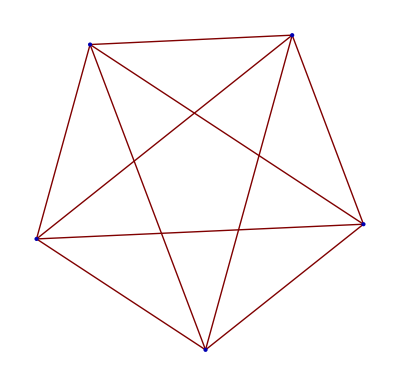

```mathematica
GraphPlot[matrizadyacencia]
```

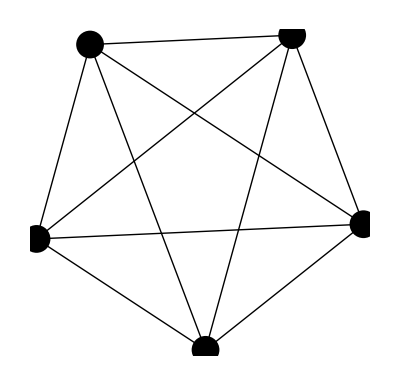

```mathematica
GraphPlot[F,PlotStyle->{Black,PointSize[.05]}]
```

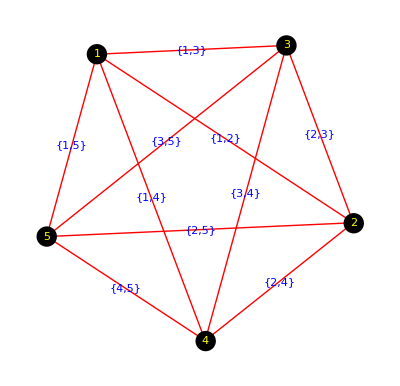

```mathematica
GraphPlot[F,VertexRenderingFunction->({Black,Disk[#,.04],Yellow,Text[#2,#]}&),EdgeRenderingFunction->({Red,Line[#1],Blue,Text[#2,{(#1[[1]][[1]]+#1[[2]][[1]])/2,(#1[[1]][[2]]+#1[[2]][[2]])/2}]}&),EdgeLabeling->True,BaseStyle->{FontSize->12}]
```

```mathematica
<<Combinatorica`
```

```mathematica
G=FromAdjacencyMatrix[matrizadyacencia]
```

⁃Graph:<10,5,Undirected>⁃

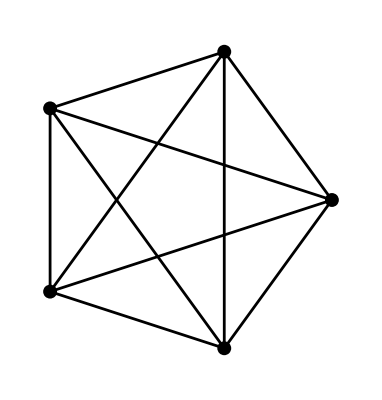

```mathematica
ShowGraph[G]
```

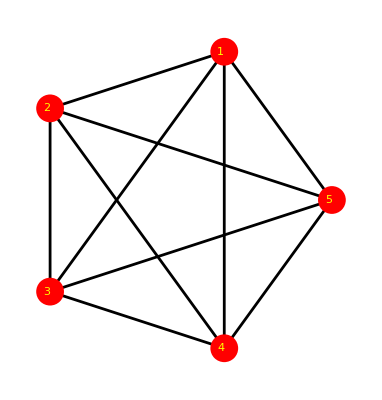

```mathematica
ShowGraph[G,VertexColor->Red, VertexStyle->PointSize[0.05],VertexNumber->True,VertexNumberColor->Yellow,VertexNumberPosition->{+.01,+.0}]
```

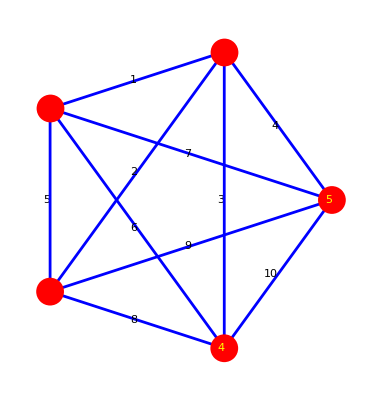

```mathematica
ShowGraph[G,VertexColor->Red, VertexStyle->PointSize[0.05],VertexNumber->True,VertexNumberColor->Yellow,VertexNumberPosition->{+.01,+.0},EdgeColor->Blue,EdgeLabel->True,EdgeColor->Blue,EdgeLabel->True]
```

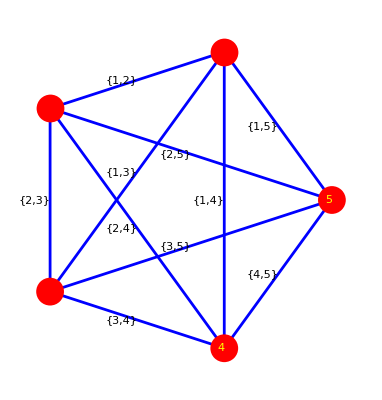

```mathematica
ShowGraph[Graph[Table[{Edges[G][[i]],EdgeLabel->Edges[G][[i]]},{i,M[G]}],G[[2]]],VertexColor->Red, VertexStyle->PointSize[0.05],VertexNumber->True,VertexNumberColor->Yellow,VertexNumberPosition->{+.01,+.0},EdgeColor->Blue,EdgeLabel->True]
```

#### Ejemplo 5.5.

```mathematica
matrizadyacencia={{0,0,0,1,1},{1,0,0,1,0},{1,0,0,0,0},{0,0,1,0,1},{0,0,1,0,0}};
```

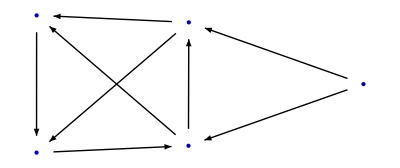

```mathematica
GraphPlot[matrizadyacencia,EdgeRenderingFunction->({Arrow[#1,0.1]}&),DirectedEdges->True]
```

```mathematica
GRAFO=matrizadyacencia;
```

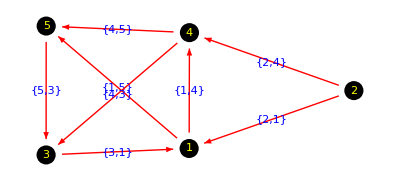

```mathematica
GraphPlot[GRAFO,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&),EdgeRenderingFunction->({Red,Arrow[#1,0.1],Blue,Text[#2,{(#1[[1]][[1]]+#1[[2]][[1]])/2,(#1[[1]][[2]]+#1[[2]][[2]])/2}]}&),BaseStyle->{FontSize->12},DirectedEdges->True]
```

```mathematica
<<Combinatorica`
```

```mathematica
G=FromAdjacencyMatrix[matrizadyacencia,Type->Directed]
```

⁃Graph:<8,5,Directed>⁃

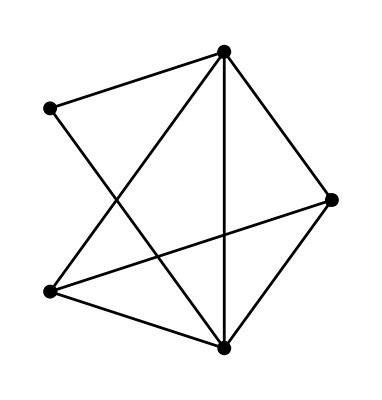

```mathematica
ShowGraph[G]
```

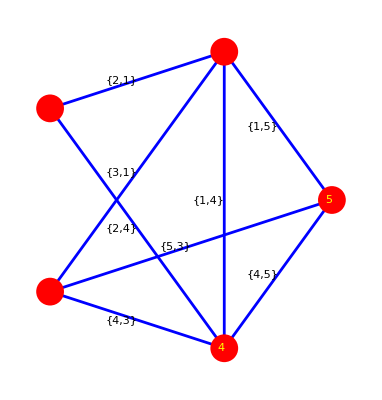

```mathematica
ShowGraph[Graph[Table[{Edges[G][[i]],EdgeLabel->Edges[G][[i]]},{i,M[G]}],G[[2]],EdgeDirection->True],VertexColor->Red, VertexStyle->PointSize[0.05],VertexNumber->True,VertexNumberColor->Yellow,VertexNumberPosition->{+.01,+.0},EdgeColor->Blue,EdgeLabel->True]
```

#### Ejemplo 5.6.

```mathematica
W={1,2,3,4,5};
F={1->2,2->3,3->4};
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{},
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[F[[k,1]],F[[k,2]]]]=1;
matrizadyacencia[[F[[k,2]],F[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

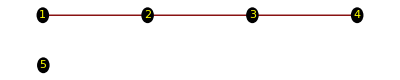

```mathematica
GRAFO=MATRIZADYACENCIA[W,F];
GraphPlot[GRAFO,VertexRenderingFunction->({Black,Disk[#,.06],Yellow,Text[#2,#1]}&)]
```

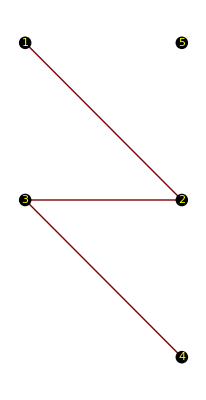

```mathematica
coordenadas={1->{0,2},2->{1,1},3->{0,1},4->{1,0},5->{1,2}};
GraphPlot[GRAFO,VertexRenderingFunction->({Black,Disk[#,.04],Yellow,Text[#2,#1]}&),VertexCoordinateRules->coordenadas]
```

```mathematica
<<Combinatorica`
```

```mathematica
G=FromAdjacencyMatrix[GRAFO]
```

⁃Graph:<3,5,Undirected>⁃

```mathematica
NuevoG=Graph[G[[1]],{{{0,2}},{{1,1}},{{0,1}},{{1,0}},{{1,2}}}]
```

⁃Graph:<3,5,Undirected>⁃

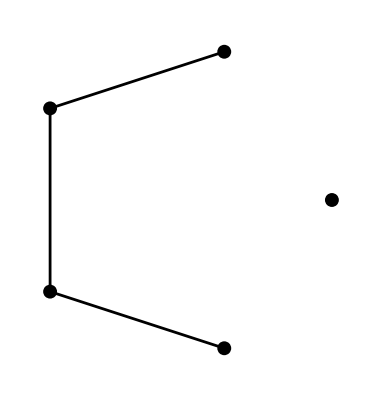

```mathematica
ShowGraph[G]
```

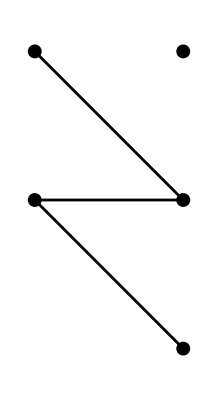

```mathematica
ShowGraph[NuevoG]
```

## 4. GRAFOS ISOMORFOS

#### Programa 5.7. Isomorfismos de grafos no orientados

W1=CONJUNTO DE VÉRTICES DEL PRIMER GRAFO;
F1=CONJUNTO DE LADOS DEL PRIMER GRAFO;
W2=CONJUNTO DE VÉRTICES DEL SEGUNDO GRAFO;
F2=CONJUNTO DE LADOS DEL SEGUNDO GRAFO;
DEFINICIÓN DE LA APLICACIÓN funcion[] ENTRE LOS CONJUNTOS DE VÉRTICES;

Isomorfismo=True;
If[Length[W1]==Length[Table[funcion[W1[[i]]],{i,Length[W1]}]] && Length[W1]==Length[W2],   
  Do[
            If[Length[Intersection[{funcion[F1[[i]][[1]]]->funcion[F1[[i]][[2]]]},F2]]==1,,Isomorfismo=False;];
         ,{i,Length[F1]}];,
  Isomorfismo=False;
  ];
  Isomorfismo

#### Programa 5.8. Isomorfismos de grafos dirigidos

W1=CONJUNTO DE VÉRTICES DEL PRIMER GRAFO;
F1=CONJUNTO DE FLECHAS DEL PRIMER GRAFO;
W2=CONJUNTO DE VÉRTICES DEL SEGUNDO GRAFO;
F2=CONJUNTO DE FLECHAS DEL SEGUNDO GRAFO;
DEFINICIÓN DE LA APLICACIÓN funcion[] ENTRE LOS CONJUNTOS DE VÉRTICES;

Isomorfismo=True;
If[Length[W1]==Length[Table[funcion[W1[[i]]],{i,Length[W1]}]] && Length[W1]==Length[W2]&& Length[F1]==Length[F2],   
  Do[
            If[Length[Intersection[{funcion[F1[[i]][[1]]]->funcion[F1[[i]][[2]]],funcion[F1[[i]][[2]]]->funcion[F1[[i]][[1]]]},F2]]==1,,Isomorfismo=False;];
         ,{i,Length[F1]}];,
  Isomorfismo=False;
  ];
  Isomorfismo

#### Ejemplo 5.7.

```mathematica
W1={1,2,3,4,5};
W2={1,2,3,4,5};
F1={1->2,1->4,1->5,2->3,2->5,3->4,3->5,4->5};
F2={1->2,1->3,1->4,1->5,2->3,2->5,3->4,4->5};
funcion[1]=4;
funcion[2]=5;
funcion[3]=2;
funcion[4]=3;
funcion[5]=1;
```

NO ORIENTADO

```mathematica
Isomorfismo=True;
If[Length[W1]==Length[Table[funcion[W1[[i]]],{i,Length[W1]}]] && Length[W1]==Length[W2]&& Length[F1]==Length[F2],   
Do[
      If[Length[Intersection[{funcion[F1[[i]][[1]]]->funcion[F1[[i]][[2]]],funcion[F1[[i]][[2]]]->funcion[F1[[i]][[1]]]},F2]]==1,,Isomorfismo=False;];
   ,{i,Length[F1]}];,
Isomorfismo=False;
];Isomorfismo
```

True

DIRIGIDO

```mathematica
Isomorfismo=True;
If[Length[W1]==Length[Table[funcion[W1[[i]]],{i,Length[W1]}]] && Length[W1]==Length[W2],   
Do[
      If[Length[Intersection[{funcion[F1[[i]][[1]]]->funcion[F1[[i]][[2]]]},F2]]==1,,Isomorfismo=False;];
   ,{i,Length[F1]}];,
Isomorfismo=False;
];Isomorfismo
```

False

#### Función 5.9. ISOMORFAS[]

```mathematica
ISOMORFAS[A_]:=Module[{j,matricesP},
isomorfas={};
matricesP=Permutations[IdentityMatrix[Dimensions[A][[1]]]];
Do[
isomorfas=Union[isomorfas,{matricesP[[j]].A.Transpose[matricesP[[j]]]}];
,{j,Length[matricesP]}];
isomorfas
];
```

#### Función 5.10. ISOMORFOS[]

```mathematica
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   
matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   
Do[	      
If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
Print["Son isomorfos, una matriz P es: ",MatrixForm[matrizP], 
      ", una permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
```

#### Ejemplo 5.8.

```mathematica
ISOMORFAS[A_]:=Module[{j,matricesP},
isomorfas={};
matricesP=Permutations[IdentityMatrix[Dimensions[A][[1]]]];
Do[
isomorfas=Union[isomorfas,{matricesP[[j]].A.Transpose[matricesP[[j]]]}];
,{j,Length[matricesP]}];
isomorfas
];
```

```mathematica
ISOMORFAS[{{0,1,0,0},{1,0,0,1},{0,0,0,1},{0,1,1,0}}]
```

{{{0,0,0,1},{0,0,1,0},{0,1,0,1},{1,0,1,0}},{{0,0,0,1},{0,0,1,1},{0,1,0,0},{1,1,0,0}},{{0,0,1,0},{0,0,0,1},{1,0,0,1},{0,1,1,0}},{{0,0,1,0},{0,0,1,1},{1,1,0,0},{0,1,0,0}},{{0,0,1,1},{0,0,0,1},{1,0,0,0},{1,1,0,0}},{{0,0,1,1},{0,0,1,0},{1,1,0,0},{1,0,0,0}},{{0,1,0,0},{1,0,0,1},{0,0,0,1},{0,1,1,0}},{{0,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,0}},{{0,1,0,1},{1,0,0,0},{0,0,0,1},{1,0,1,0}},{{0,1,0,1},{1,0,1,0},{0,1,0,0},{1,0,0,0}},{{0,1,1,0},{1,0,0,0},{1,0,0,1},{0,0,1,0}},{{0,1,1,0},{1,0,0,1},{1,0,0,0},{0,1,0,0}}}

```mathematica
Table[MatrixForm[isomorfas[[i]]],{i,Length[isomorfas]}]
```

{(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 0 | 0
1 | 1 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0),(0 | 0 | 1 | 0
0 | 0 | 1 | 1
1 | 1 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 0 | 1
1 | 0 | 0 | 0
1 | 1 | 0 | 0),(0 | 0 | 1 | 1
0 | 0 | 1 | 0
1 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 1 | 1 | 0),(0 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 1 | 0),(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 1 | 1 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 1 | 0),(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)}

#### Ejemplo 5.9.

```mathematica
A1={{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0}};
A2={{0,1,1,0,1,0},{1,0,0,1,1,0},{1,0,0,1,0,1},{0,1,1,0,0,1},{1,1,0,0,0,1},{0,0,1,1,1,0}};
A3={{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}};
A4={{0,1,1,0,0,1},{1,0,1,0,1,0},{1,1,0,1,0,0},{0,0,1,0,1,1},{0,1,0,1,0,1},{1,0,0,1,1,0}};
A5={{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0}};
A6={{0,1,1,1,0,0},{1,0,1,0,0,1},{1,1,0,0,1,0},{1,0,0,0,1,1},{0,0,1,1,0,1},{0,1,0,1,1,0}};
```

```mathematica
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   Do[	      
      If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
         Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
   Print["Son isomorfos, una matriz P es: ",MatrixForm[matrizP], 
      ", una permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
```

```mathematica
ISOMORFOS[A1,A2]
```

No son isomorfos

```mathematica
ISOMORFOS[A1,A3]
```

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 4 | 2 | 5 | 3 | 6)

```mathematica
ISOMORFOS[A1,A4]
```

No son isomorfos

```mathematica
ISOMORFOS[A1,A5]
```

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 3 | 4 | 5 | 6)

```mathematica
ISOMORFOS[A1,A6]
```

No son isomorfos

```mathematica
ISOMORFOS[A2,A4]
```

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 5 | 6 | 4 | 3)

```mathematica
ISOMORFOS[A2,A6]
```

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 5 | 3 | 6 | 4)

```mathematica
<<Combinatorica`
```

```mathematica
G1=FromAdjacencyMatrix[A1];
G2=FromAdjacencyMatrix[A2];
G3=FromAdjacencyMatrix[A3];
G4=FromAdjacencyMatrix[A4];
G5=FromAdjacencyMatrix[A5];
G6=FromAdjacencyMatrix[A6];
```

```mathematica
IsomorphicQ[G1,G2]
```

False

```mathematica
IsomorphicQ[G1,G3]
```

True

```mathematica
Isomorphism[G1,G3]
```

{1,3,5,2,4,6}

```mathematica
IsomorphicQ[G1,G4]
```

False

```mathematica
IsomorphicQ[G1,G5]
```

True

```mathematica
Isomorphism[G1,G5]
```

{1,2,3,4,5,6}

```mathematica
IsomorphicQ[G1,G6]
```

False

```mathematica
IsomorphicQ[G2,G4]
```

True

```mathematica
Isomorphism[G2,G4]
```

{1,2,6,5,3,4}

```mathematica
IsomorphicQ[G2,G6]
```

True

```mathematica
Isomorphism[G2,G6]
```

{1,2,4,6,3,5}

```mathematica
Isomorphism[G2,G6,All]
```

{{1,2,4,6,3,5},{1,3,4,5,2,6},{2,1,6,4,3,5},{2,3,6,5,1,4},{3,1,5,4,2,6},{3,2,5,6,1,4},{4,5,1,3,6,2},{4,6,1,2,5,3},{5,4,3,1,6,2},{5,6,3,2,4,1},{6,4,2,1,5,3},{6,5,2,3,4,1}}

#### Ejemplo 5.10.

```mathematica
A1={{0,0,0,1},{1,0,0,0},{1,1,0,0},{0,1,1,0}};
A2={{0,0,0,1},{1,0,1,0},{1,0,0,0},{0,1,1,0}};
A3={{0,0,0,1},{1,0,0,1},{1,1,0,0},{0,0,0,1}};
```

```mathematica
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   Do[	      
      If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
         Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
   Print["Son isomorfos, una matriz P es: ",MatrixForm[matrizP], 
      ", una permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
```

```mathematica
ISOMORFOS[A1,A2]
```

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4
1 | 3 | 2 | 4)

```mathematica
ISOMORFOS[A1,A3]
```

No son isomorfos

```mathematica
<<Combinatorica`
```

```mathematica
G1=FromAdjacencyMatrix[A1,Type->Directed];
G2=FromAdjacencyMatrix[A2,Type->Directed];
G3=FromAdjacencyMatrix[A3,Type->Directed];
```

```mathematica
IsomorphicQ[G1,G2]
```

True

```mathematica
Isomorphism[G1,G2]
```

{1,3,2,4}

```mathematica
IsomorphicQ[G1,G3]
```

False

### 4.1. EFICACIA Y OPTIMIZACIÓN

#### Ejemplo 5.11.

```mathematica
A1={{0,0,1,1,0,0,0,0,0},{0,0,1,0,0,1,0,0,0},{1,1,0,1,1,1,0,0,0},{1,0,1,0,1,0,1,1,0},{0,0,1,1,0,1,1,0,0},{0,1,1,0,1,0,1,0,1},{0,0,0,1,1,1,0,1,1},{0,0,0,1,0,0,1,0,0},{0,0,0,0,0,1,1,0,0}};
A2={{0,0,1,1,1,0,0,0,0},{0,0,1,0,1,1,0,0,0},{1,1,0,1,0,1,0,0,0},{1,0,1,0,0,0,1,1,0},{1,1,0,0,0,0,1,0,1},{0,1,1,0,0,0,0,1,1},{0,0,0,1,1,0,0,1,0},{0,0,0,1,0,1,1,0,1},{0,0,0,0,1,1,0,1,0}};
```

```mathematica
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   Do[	      
      If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
         Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
   Print["Son isomorfos, la matriz P es: ",MatrixForm[matrizP], 
      ", la permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
```

```mathematica
Timing[ISOMORFOS[A1,A2]][[1]]
```

No son isomorfos

41.609

```mathematica
Timing[Eigenvalues[A1]==Eigenvalues[A2]]
```

{1.02696×10^-15,False}

```mathematica
n=2;
B1=MatrixPower[A1,n];B2=MatrixPower[A2,n];
```

```mathematica
Timing[n=2;
B1=MatrixPower[A1,n];B2=MatrixPower[A2,n];
Sort[Table[B1[[i,i]],{i,Dimensions[B1][[1]]}]]==Sort[Table[B2[[i,i]],{i,Dimensions[B2][[1]]}]]]
```

{0.,False}

#### Ejemplo 5.12.

```mathematica
Eigenvalues[{{0,1,1,0,0},{1,0,0,1,0},{1,0,0,1,0},{0,1,1,0,0},{0,0,0,0,0}}]
```

{-2,2,0,0,0}

```mathematica
Eigenvalues[{{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0}}]
```

{-2,2,0,0,0}

#### Ejemplo 5.13.

```mathematica
A1={{0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}};
```

```mathematica
A2={{0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}};
```

```mathematica
Sort[Table[MatrixPower[A1,2][[i1,i1]],{i1,16}]]==Sort[Table[MatrixPower[A2,2][[i1,i1]],{i1,16}]]
Sort[Table[MatrixPower[A1,3][[i1,i1]],{i1,16}]]==Sort[Table[MatrixPower[A2,3][[i1,i1]],{i1,16}]]
Sort[Table[MatrixPower[A1,4][[i1,i1]],{i1,16}]]==Sort[Table[MatrixPower[A2,4][[i1,i1]],{i1,16}]]
Sort[Table[MatrixPower[A1,5][[i1,i1]],{i1,16}]]==Sort[Table[MatrixPower[A2,5][[i1,i1]],{i1,16}]]
```

True

True

True

«1 more identical outputs»

```mathematica
Sort[Table[MatrixPower[A1,6][[i1,i1]],{i1,16}]]==Sort[Table[MatrixPower[A2,6][[i1,i1]],{i1,16}]]
```

False

```mathematica
Eigenvalues[A1]==Eigenvalues[A2]
```

False

#### Función 5.11. ISOMORFOS2[]

```mathematica
ISOMORFOS2[A1_,A2_]:=Module[{potencias,n,permutaciones2,adyacentes1,tabla1,tabla2,condicion,imagenes,i,j,k,h,kk},
potencias=3;
n=Dimensions[A1][[1]];
tabla1=Table[Table[MatrixPower[A1,i+1][[j,j]],{i,potencias}],{j,Dimensions[A1][[1]]}];
tabla2=Table[Table[MatrixPower[A2,i+1][[j,j]],{i,potencias}],{j,Dimensions[A2][[1]]}];
If[Sort[tabla1]==Sort[tabla2] && Eigenvalues[A1]==Eigenvalues[A2],
permutaciones=Position[tabla2,tabla1[[1]]];
Do[

permutaciones2={};
adyacentes1=Position[A1[[i]],1];

Do[
imagenes=Complement[Position[tabla2,tabla1[[i]]],Table[{permutaciones[[j]][[kk]]},{kk,Length[permutaciones[[j]]]}]];
Do[
condicion=True;

Do[

If[adyacentes1[[k]][[1]]<i,

If[A2[[permutaciones[[j]][[adyacentes1[[k]][[1]]]],imagenes[[h]][[1]]]]!=1,condicion=False;Break[];];
];
,{k,Length[adyacentes1]}];

If[condicion,
permutaciones2=Join[permutaciones2,{Join[permutaciones[[j]],{imagenes[[h]][[1]]}]}];
];

,{h,Length[imagenes]}];
If[Mod[j,1000]==0,Print["Van ",j,",  ",Length[permutaciones2]];];
,{j,Length[permutaciones]}];
permutaciones=permutaciones2;

,{i,2,n}];
Print["PERMUTACIONES:"];
Print[Table[MatrixForm[{Table[j,{j,n}],permutaciones[[i]]}],{i,Length[permutaciones]}]];
,
permutaciones={};
];
If[permutaciones=={},False,True]];
```

#### Ejemplo 5.14.

```mathematica
A1={{0,0,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1},{1,1,0,1,0,0,1,0,1},
{1,1,1,0,1,0,0,0,1},{1,1,0,1,0,1,0,0,1},{1,1,0,0,1,0,0,1,1},{1,1,1,0,0,0,0,1,1},
{1,1,0,0,0,1,1,0,1},{1,1,1,1,1,1,1,1,0}};
A2={{0,1,1,1,1,1,1,1,0},{1,0,1,0,0,1,0,1,1},{1,1,0,1,0,1,0,0,1},
{1,0,1,0,1,1,0,0,1},{1,0,0,1,0,1,1,0,1},{1,1,1,1,1,0,1,1,1},{1,0,0,0,1,1,0,1,1},
{1,1,0,0,0,1,1,0,1},{0,1,1,1,1,1,1,1,0}};
```

```mathematica
ISOMORFOS2[A1_,A2_]:=Module[{potencias,n,permutaciones2,adyacentes1,tabla1,tabla2,condicion,imagenes,i,j,k,h,kk},
potencias=3;
n=Dimensions[A1][[1]];
tabla1=Table[Table[MatrixPower[A1,i+1][[j,j]],{i,potencias}],{j,Dimensions[A1][[1]]}];
tabla2=Table[Table[MatrixPower[A2,i+1][[j,j]],{i,potencias}],{j,Dimensions[A2][[1]]}];
If[Sort[tabla1]==Sort[tabla2] && Eigenvalues[A1]==Eigenvalues[A2],
permutaciones=Position[tabla2,tabla1[[1]]];
Do[

permutaciones2={};
adyacentes1=Position[A1[[i]],1];

Do[
imagenes=Complement[Position[tabla2,tabla1[[i]]],Table[{permutaciones[[j]][[kk]]},{kk,Length[permutaciones[[j]]]}]];
Do[
condicion=True;

Do[

If[adyacentes1[[k]][[1]]<i,

If[A2[[permutaciones[[j]][[adyacentes1[[k]][[1]]]],imagenes[[h]][[1]]]]!=1,condicion=False;Break[];];
];
,{k,Length[adyacentes1]}];

If[condicion,
permutaciones2=Join[permutaciones2,{Join[permutaciones[[j]],{imagenes[[h]][[1]]}]}];
];

,{h,Length[imagenes]}];
If[Mod[j,1000]==0,Print["Van ",j,",  ",Length[permutaciones2]];];
,{j,Length[permutaciones]}];
permutaciones=permutaciones2;

,{i,2,n}];
Print["PERMUTACIONES:"];
Print[Table[MatrixForm[{Table[j,{j,n}],permutaciones[[i]]}],{i,Length[permutaciones]}]];
,
permutaciones={};
];
If[permutaciones=={},False,True]];
```

```mathematica
Timing[ISOMORFOS2[A1,A2]]
```

PERMUTACIONES:

{(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 2 | 3 | 4 | 5 | 8 | 7 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 2 | 8 | 7 | 5 | 3 | 4 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 3 | 2 | 8 | 7 | 4 | 5 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 3 | 4 | 5 | 7 | 2 | 8 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 4 | 3 | 2 | 8 | 5 | 7 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 4 | 5 | 7 | 8 | 3 | 2 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 5 | 4 | 3 | 2 | 7 | 8 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 5 | 7 | 8 | 2 | 4 | 3 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 7 | 5 | 4 | 3 | 8 | 2 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 7 | 8 | 2 | 3 | 5 | 4 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 8 | 2 | 3 | 4 | 7 | 5 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 9 | 8 | 7 | 5 | 4 | 2 | 3 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 2 | 3 | 4 | 5 | 8 | 7 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 2 | 8 | 7 | 5 | 3 | 4 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 3 | 2 | 8 | 7 | 4 | 5 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 3 | 4 | 5 | 7 | 2 | 8 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 4 | 3 | 2 | 8 | 5 | 7 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 4 | 5 | 7 | 8 | 3 | 2 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 5 | 4 | 3 | 2 | 7 | 8 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 5 | 7 | 8 | 2 | 4 | 3 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 7 | 5 | 4 | 3 | 8 | 2 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 7 | 8 | 2 | 3 | 5 | 4 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 8 | 2 | 3 | 4 | 7 | 5 | 6),(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
9 | 1 | 8 | 7 | 5 | 4 | 2 | 3 | 6)}

{0.094,True}

```mathematica
MemoryInUse[]
```

7383472

```mathematica
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],
matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];
Do[
If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
         Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
   Print["Son isomorfos, la matriz P es: ",MatrixForm[matrizP], 
      ", la permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
```

```mathematica
Timing[ISOMORFOS[A1,A2]]
```

Son isomorfos, la matriz P es: (1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0), la permutación es: (1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
1 | 3 | 4 | 5 | 6 | 9 | 8 | 7 | 2)

{1.25,Null}

```mathematica
MemoryInUse[]
```

7396608

```mathematica
matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];
```

```mathematica
Length[matricesP]
```

362880

#### Ejemplo 5.15.

```mathematica
A1={{0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}};
```

```mathematica
A2={{0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}};
```

```mathematica
ISOMORFOS2[A1_,A2_]:=Module[{potencias,n,permutaciones2,adyacentes1,tabla1,tabla2,condicion,imagenes,i,j,k,h,kk},
potencias=3;
n=Dimensions[A1][[1]];
tabla1=Table[Table[MatrixPower[A1,i+1][[j,j]],{i,potencias}],{j,Dimensions[A1][[1]]}];
tabla2=Table[Table[MatrixPower[A2,i+1][[j,j]],{i,potencias}],{j,Dimensions[A2][[1]]}];
If[Sort[tabla1]==Sort[tabla2] && Eigenvalues[A1]==Eigenvalues[A2],
permutaciones=Position[tabla2,tabla1[[1]]];
Do[

permutaciones2={};
adyacentes1=Position[A1[[i]],1];

Do[
imagenes=Complement[Position[tabla2,tabla1[[i]]],Table[{permutaciones[[j]][[kk]]},{kk,Length[permutaciones[[j]]]}]];
Do[
condicion=True;

Do[

If[adyacentes1[[k]][[1]]<i,

If[A2[[permutaciones[[j]][[adyacentes1[[k]][[1]]]],imagenes[[h]][[1]]]]!=1,condicion=False;Break[];];
];
,{k,Length[adyacentes1]}];

If[condicion,
permutaciones2=Join[permutaciones2,{Join[permutaciones[[j]],{imagenes[[h]][[1]]}]}];
];

,{h,Length[imagenes]}];
If[Mod[j,1000]==0,Print["Van ",j,",  ",Length[permutaciones2]];];
,{j,Length[permutaciones]}];
permutaciones=permutaciones2;

,{i,2,n}];
Print["PERMUTACIONES:"];
Print[Table[MatrixForm[{Table[j,{j,n}],permutaciones[[i]]}],{i,Length[permutaciones]}]];
,
permutaciones={};
];
If[permutaciones=={},False,True]];
```

```mathematica
Timing[ISOMORFOS2[A1,A2]]
```

{0.094,False}

```mathematica
MemoryInUse[]
```

29233608

```mathematica
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   Do[	      
      If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
         Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
   Print["Son isomorfos, la matriz P es: ",MatrixForm[matrizP], 
      ", la permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
```

```mathematica
Timing[ISOMORFOS[A1,A2]]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
<<Combinatorica`
```

```mathematica
G1=FromAdjacencyMatrix[A1];
G2=FromAdjacencyMatrix[A2];
```

```mathematica
Timing[Isomorphism[G1,G2]]
```

{0.,{}}

#### Observación

```mathematica
<<Combinatorica`
```

```mathematica
n=60
A1=ToAdjacencyMatrix[RandomGraph[n,.5]];
P=Permute[IdentityMatrix[n],RandomSample[Range[n]]];
A2=P.A1.Transpose[P];
```

60

{{0,0,1,1,1,1,0,1,1,0,0,0,0,0,1,0,0,0,1,0,1,1,1,0,1,0,0,1,0,0,0,1,1,1,0,1,1,0,1,1,0,1,0,1,0,1,0,0,1,1,0,0,0,0,0,1,1,1,0,0},{0,0,0,1,0,0,1,1,0,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,0,0,1,1,0,1,0,1,1,0,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,1,1,1,0,1},{1,0,0,0,0,0,1,1,1,0,1,1,0,1,1,0,1,0,1,1,1,0,1,1,1,0,0,0,1,1,1,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,1,1,1,1,0,1,1,0,1},{1,1,0,0,0,1,0,1,0,0,1,0,1,1,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,1,1,1,1,0,0,1,1,1,1,0,1,0,0,0,1,1,0,0},{1,0,0,0,0,0,0,0,1,1,0,1,1,1,0,1,0,1,0,1,1,0,1,1,1,0,1,0,1,0,0,1,0,0,1,1,1,1,0,1,1,1,0,0,1,1,1,1,0,0,0,1,0,1,1,0,1,1,1,1},{1,0,0,1,0,0,1,0,0,1,1,1,0,1,1,0,1,0,1,0,0,0,1,0,1,1,1,0,1,1,0,0,1,1,1,1,1,1,0,1,0,1,0,0,0,1,0,1,1,1,1,1,1,0,1,1,0,1,1,1},{0,1,1,0,0,1,0,0,1,0,0,1,0,1,1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,0,1,0,1,1,1,0,0,0,0,1,1,1,0,1,0,1,0,1,0,0,1,1,0,1,0},{1,1,1,1,0,0,0,0,1,0,1,1,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,0,0,1,1,0,0,0,0,1},{1,0,1,0,1,0,1,1,0,1,0,1,0,0,0,0,0,1,1,0,1,1,1,0,0,1,0,0,0,1,0,1,1,0,0,1,1,0,1,1,0,0,0,0,0,1,1,0,0,0,1,0,0,1,1,0,1,1,1,1},{0,0,0,0,1,1,0,0,1,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,1,0,0,1,1,0,1,1,0,0,0,1,1,0,1,1,1,1,1,0,0,0,0,1,1,0,1,1},{0,1,1,1,0,1,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,0,1,0,1,0,0,1,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,1,1,0,0,0,1,1,0,1,1,1,1,1},{0,1,1,0,1,1,1,1,1,0,0,0,0,1,0,0,1,0,1,0,1,1,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,1,1,1,1,0,0,1,1,1,1,0,0,0,1,0,1,0,0,0,1,1,1,0},{0,1,0,1,1,0,0,1,0,0,1,0,0,1,1,1,1,1,1,1,0,1,1,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,1,1,1,1,0,0,1,0,1,1,0,0,1,0,0,1,1,0,1,1},{0,0,1,1,1,1,1,0,0,0,0,1,1,0,1,1,0,0,1,1,1,0,0,0,1,1,1,1,1,1,1,0,0,1,1,0,1,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,1,0,1,0,0,1,1},{1,1,1,1,0,1,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,1,1,0,0,1,1,1,0,1,1,1,0,0,0,1,0,1,0,0,1,1,1,0,1,1,1,1,1},{0,1,0,0,1,0,0,0,0,0,1,0,1,1,0,0,0,1,0,1,0,1,0,0,0,0,1,1,0,0,1,0,0,1,0,0,0,1,1,0,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,1,1,0,0,1},{0,0,1,0,0,1,1,0,0,1,0,1,1,0,0,0,0,0,1,1,0,1,1,0,1,1,1,0,1,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,1,0,1,0,1,1,1,0,0,1,1,1,1,0,0,0},{0,0,0,1,1,0,1,0,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,1,1,0,1,0,1,1,0,1,0,0,0,1,0,0,1,1,0,0,1,0,0,1,1,0},{1,0,1,0,0,1,0,0,1,0,0,1,1,1,0,0,1,0,0,0,0,1,1,0,1,0,0,1,0,0,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,0,1,1,0,0,1,1,0,1,0,0,0,0,1,0},{0,0,1,0,1,0,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,0,0,1,1,0,0,0,0,0,1,1,1,0,1,1,0,1,0,1,0,0,1,1,1,0,0,1,0},{1,0,1,0,1,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,1,0,1,0,0,1,1,0,0,0,0,1,1,1,1,1,1,0,1,1,1,1,0,0,0,0,1,0,1,0},{1,0,0,1,0,0,0,1,1,0,0,1,1,0,0,1,1,0,1,1,1,0,1,1,1,0,1,0,1,0,0,1,1,1,0,1,1,1,0,0,0,0,1,1,0,1,0,0,1,1,1,0,1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1,1,0,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0,1,1,1,1,0,1,0,1,1,1,0,1,0,1,0,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,1,1},{0,0,1,0,1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,0,1,1,0,1,1,0,0,0,0,1,0,0,1,1,0,1,0,0,1,0,1,1,0,0,1,0,1,0},{1,1,1,1,1,1,0,1,0,0,1,0,1,1,0,0,1,1,1,0,1,1,0,1,0,0,0,0,1,1,0,1,0,1,0,0,1,1,0,0,1,1,1,0,1,0,0,0,1,0,0,1,0,0,0,0,1,1,0,1},{0,1,0,0,0,1,1,0,1,0,0,1,0,1,0,0,1,1,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,1,0,1,1,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1},{0,1,0,0,1,1,1,1,0,1,0,0,0,1,0,1,1,0,0,1,1,1,1,1,0,1,0,1,1,1,1,0,1,0,0,1,0,1,0,1,1,1,1,1,0,0,1,1,0,1,0,0,0,1,1,0,0,0,1,0},{1,0,0,0,0,0,0,1,0,1,1,0,0,1,1,1,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,1,1,1,1,0,0,1,0,1,0,1,1,0,1,1,0,0,1,0,1,1,0,0,1,1,1,1,0,1},{0,0,1,0,1,1,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1,1,1,0,1,0,1,0,0,1,0,1,1,1,0,0,1,0,1,1,1,1,0,1,1,0,0,0,0,1,0,1,1,1,1,1,0,1,0,1},{0,0,1,0,0,1,0,1,1,1,0,1,0,1,1,0,0,0,0,1,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,0,0,0,0,1,1,1,1,1,0,1,0,0,1,0,1,0,1},{0,1,1,1,0,0,0,1,0,0,1,0,0,1,0,1,0,0,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,1,0,1,1,1,1,0,1,0,0,0,1,1,1,0,1,0,0,0,1,1,0,0,1,1,0,1},{1,1,1,0,1,0,1,1,1,0,1,0,1,0,0,0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,1,0,1,1,0,0,1,1,0,1,1,1,1,0,1,0,1,1,0,1,0,0,0,0,0,1,0,0,0,1},{1,0,0,0,0,1,0,1,1,1,1,1,0,0,1,0,0,1,1,0,1,1,1,1,0,0,1,1,1,1,1,1,0,1,0,0,1,1,0,0,1,1,1,0,1,1,0,0,1,0,0,1,1,0,1,1,0,1,0,1},{1,1,1,0,0,1,0,1,0,0,0,1,1,1,1,1,1,1,0,0,0,1,1,1,1,0,0,1,1,0,1,1,1,0,0,0,1,1,1,0,1,1,0,1,0,1,1,1,1,0,1,1,0,0,0,0,0,0,0,1},{0,0,0,0,1,1,0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0,1,0,1,0,0,0,0,0,1,1,0,1,1,0,1,1,0,1,0,1,0,1,0,0,1,0,0,1,1,0,0,0,1},{1,1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,1,0,1,1,1,0,1,0,0,1,0,0,1,1,0,0,0,1,0,0,1,0,0,0,1,0,0,1,1,0,1,0,0,1,1,1,1,1,1,1,0,0,0},{1,1,0,0,1,1,0,1,1,1,0,0,0,1,1,0,0,1,1,0,1,1,1,1,1,1,0,0,1,0,1,1,1,1,1,0,0,1,0,1,1,1,1,0,0,0,0,1,0,0,0,1,1,0,0,1,1,1,1,1},{0,0,0,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,1,0,0,1,0,0,1,1,1,1,0,1,1,1,1,1,0,1,1,0,0,0,0,1,1,1,0,1,0,0,0,1,0,1,0,0,0,1,1,0,1,0},{1,1,0,1,0,0,1,1,1,1,0,1,1,0,1,1,0,1,1,0,0,0,1,0,0,0,0,0,1,0,1,0,0,1,1,0,0,0,0,1,0,0,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0,1,0},{1,1,0,0,1,1,1,0,1,1,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,1,1,1,1,0,0,1,0,0,1,0,1,0,1,0,1,1,1,0,1,1,0,0,0,0,1,1,1,1,1,0,1,1,0,0},{0,1,0,0,1,0,0,1,0,0,0,1,1,0,1,1,0,1,1,0,0,0,1,0,1,0,1,0,1,1,1,1,1,1,0,0,1,0,0,1,0,1,0,1,1,0,0,1,1,1,1,0,0,0,1,0,0,1,0,0},{1,0,0,1,1,1,0,1,0,0,0,0,1,0,1,0,0,1,0,1,1,0,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,0,1,1,0,0,1,0,0,0,1,1,1,1,0,1,1,1,0,0,0,0,1},{0,1,1,1,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,1,1,0,0,1,1,1,1,0,0,0,1,1,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,1,1,1,1,0},{1,0,0,1,0,0,0,1,0,1,0,1,1,0,0,0,1,1,0,1,1,1,0,0,0,1,1,0,1,0,0,0,0,1,0,0,0,1,1,0,1,1,0,0,0,1,1,0,0,1,0,1,1,0,0,0,1,1,1,0},{0,1,0,1,1,0,1,1,0,1,1,1,0,1,0,1,1,0,0,0,1,0,0,1,1,1,0,1,1,0,1,1,1,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,0,0,1,1,1,0,1,0},{1,1,0,0,1,1,1,1,1,0,1,1,0,0,0,0,0,0,0,1,1,1,0,1,0,0,0,1,0,0,1,0,1,1,0,1,0,1,1,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0},{0,1,0,0,1,0,1,0,1,1,0,1,1,0,1,1,1,0,1,1,1,0,0,0,0,1,1,0,0,1,1,1,0,1,1,0,0,0,1,0,0,0,1,1,0,0,0,1,1,0,1,0,1,0,0,0,0,1,1,1},{0,0,1,1,1,1,0,1,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,1,0,1,0,1,1,0,0,0,1,1,0,0,0,1,1,0,1,0,0,0,0,0,0,1,1,1,0,0},{1,0,0,1,0,1,1,1,0,1,1,0,1,1,1,0,1,0,0,1,1,1,1,0,1,1,0,1,0,1,1,0,1,1,1,0,0,0,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,0,0,1,1,1,0,1},{1,0,0,1,0,1,0,1,0,1,0,0,1,1,0,1,1,0,0,0,1,1,1,0,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,0,1,1,0,1,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0},{0,0,1,1,0,1,1,1,1,1,0,1,0,1,0,0,1,1,1,1,1,1,0,1,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,1,1,0,0,0,0,1,0,1,1,0,1,1,0,1,1,1,0,0,1},{0,1,1,0,1,1,0,0,0,0,0,0,0,0,1,1,0,1,1,0,1,0,1,0,1,0,0,1,1,0,0,0,1,1,1,1,1,1,0,1,0,0,1,1,1,0,0,0,1,0,1,0,0,1,0,0,0,1,1,0},{0,0,1,1,0,1,1,0,0,0,1,1,1,0,1,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,1,0,1,0,0,1,1,0,0,1,0,1,1,1,0,0,1,0,0,1,1,0,0,0,0,0,1,1,0,0},{0,1,1,0,1,0,0,1,1,0,1,0,0,1,1,0,1,0,1,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,1,0,0,1,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0,1,1,0,1,0,1,0,0,0,1,1,1,1,0,0,0,1,0,1,1,0,0,0,1,1,1,0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,1,1},{1,1,0,0,0,1,1,0,0,1,1,0,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,1,1,1,0,1,1,0,1,1,1,1,0,0,0,0,1,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,1},{1,1,1,1,1,0,1,0,1,1,1,1,1,0,1,1,1,0,0,0,1,1,0,1,1,1,0,1,0,0,1,0,0,0,0,1,1,1,0,1,0,0,1,1,1,0,0,1,1,0,1,0,1,1,1,0,0,1,1,0},{1,1,1,1,1,1,0,0,1,0,1,1,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,1,1,1,1,0,1,0,0,0,1,0,0,1,1,0,1,1,0,0,1,1,1,1,0,1,1,1,0,0,1,0,1,1},{0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,1,0,0,0,0,1,0,1,1,0,1,1,0,0},{0,1,1,0,1,1,0,1,1,1,1,0,1,1,1,1,0,0,0,0,0,1,1,0,1,1,0,1,1,1,1,1,1,1,1,0,1,0,0,0,0,1,0,0,0,0,1,0,1,0,1,0,0,0,1,1,0,1,0,0}}

{{0,0,0,0,0,1,0,1,1,0,0,1,0,0,0,1,1,1,0,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,1,1,0,0,0,1,1,0,1,0,1,0,0,0,0,1,0,1,0,1,1,1,1,0,1,1},{0,0,1,1,0,0,0,0,0,1,1,1,1,0,0,1,1,0,0,1,1,0,0,1,0,0,0,1,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0},{0,1,0,1,0,1,1,1,1,0,1,0,0,0,1,0,1,1,0,0,0,0,1,1,0,1,0,0,0,0,1,1,1,1,0,1,0,1,0,0,0,1,0,0,0,1,1,1,1,0,0,1,1,0,0,1,0,1,0,0},{0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,1,1,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,1,1,1,1,0,1,1,0,1,0,1,0,1,0,0,0},{0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,0,1,0,0,1,0,0,0,0,1,0,1,1,1,1,1,1,1,1,0,0,0,1,1,1,0,0,1,1,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,0,0,0,1,0,1,0,1,1,0,0,1,0,0,0,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,1,0,1,0,1,0,1,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0},{0,0,1,1,1,0,0,1,0,1,0,1,1,1,1,1,1,0,0,0,1,1,1,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0},{1,0,1,1,1,1,1,0,1,1,1,1,0,0,1,0,1,0,1,1,1,1,0,1,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1},{1,0,1,0,1,0,0,1,0,1,0,0,0,1,0,0,1,0,1,0,0,1,0,0,0,0,1,0,0,0,1,1,1,0,1,0,1,0,1,1,1,0,0,1,0,1,0,1,0,0,1,0,1,1,0,0,0,1,0,1},{0,1,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,1,1,0,0,0,1,0,1,1,1,0,0,1,1,0,0,0,1,1,0,1,1,1,0,1,1,0,1,1,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,1,1,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,0,0,0,1,1,1,0,1,0,0,1,0,1,1,1,1,0,1,1,0,1,1,1,0,0,0,1,1,1,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,1,0,1,0,1,1,1,0,1,1,0,0,1,0,1,1,1,0,1,1,1,1,0,0,1,0,1,1,1,0,0,0,0,1,0,0,1,0,0,1,1,0,0,1,1,1,0,0,0,1,1,0,1,0,1,1,1,1,0},{0,1,0,1,0,0,1,0,0,1,1,0,0,1,1,0,0,0,1,1,1,1,1,1,0,0,0,1,1,0,1,1,1,1,1,1,1,0,1,1,1,0,1,0,0,1,1,0,0,0,0,1,1,1,1,0,0,1,1,0},{0,0,0,0,0,1,1,0,1,0,0,1,1,0,0,1,1,0,0,0,0,1,0,0,0,0,1,0,0,1,1,1,0,0,0,0,1,1,1,1,1,1,0,0,0,1,1,0,0,0,1,1,1,0,0,1,0,1,0,0},{0,0,1,0,1,0,1,1,0,1,1,0,1,0,0,0,1,1,0,1,1,0,0,1,0,1,1,0,1,1,1,0,1,1,0,0,1,0,1,1,1,1,1,0,0,1,1,1,1,1,0,0,1,0,0,1,0,1,1,0},{1,1,0,0,1,1,1,0,0,1,0,1,0,1,0,0,0,0,1,0,1,0,0,1,0,1,1,1,1,1,1,0,1,1,0,1,1,1,0,0,1,1,1,1,0,0,0,0,0,1,1,0,1,1,0,0,1,1,0,1},{1,1,1,0,0,1,1,1,1,0,0,1,0,1,1,0,0,0,1,0,0,1,0,1,0,1,1,1,0,0,1,1,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,0,0,0,0,1,1,0,1,1},{1,0,1,0,1,0,0,0,0,1,1,1,0,0,1,0,0,0,0,1,0,1,0,1,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,1,1,1,1,0,1},{0,0,0,1,0,0,0,1,1,1,0,0,1,0,0,1,1,0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,0,1,1,0,1,1,0,0,1,1,1,1,0,1,0,1,0,1,0,1,0,1,1,0,0,0,1,0},{1,1,0,1,0,1,0,1,0,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,1,1,1,0,1,0,0,0,0,1,0,0,0,1,0,1,1,0,1,0,1,0,1},{1,1,0,1,1,0,1,1,0,0,0,1,1,0,1,1,0,0,1,0,0,1,1,0,1,0,0,0,0,0,1,0,0,1,1,1,0,0,1,1,1,0,0,1,0,1,1,0,0,0,0,0,1,1,0,1,1,1,0,0},{1,0,0,1,0,0,1,1,1,0,1,1,1,1,0,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,1,1,0,1,1,0,0,1,0,1,0,1,1,0,0,1,1,0,0,0,1,1,1},{1,0,1,0,0,0,1,0,0,1,1,1,1,0,0,0,0,0,0,0,1,1,0,1,1,0,1,1,0,1,1,1,0,1,0,1,1,0,0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,1,0,1,0,0,1,1},{1,1,1,0,0,0,0,1,0,0,1,0,1,0,1,1,1,1,0,1,0,0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,1,1,1,1,1},{1,0,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,1,1,0,1,1,1,0,1,0,1,1,0,1,0,0,1,0,1,1,1,0,0,0,0,0,1,0,1,0,0,1,1,0},{1,0,1,0,1,0,1,0,0,1,1,1,0,0,1,1,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,1,0,0,1,1,1,0,0,0,1,0,1,0,1,1,1,1,0,0,0,0},{1,0,0,1,0,0,0,0,1,1,0,0,0,1,1,1,1,0,0,0,0,0,1,0,0,0,0,1,1,0,0,1,1,0,1,1,0,1,1,1,0,0,1,0,1,0,0,0,1,1,1,1,0,0,1,1,0,1,0,0},{0,1,0,0,1,0,0,0,0,0,0,1,1,0,0,1,1,0,1,1,0,1,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,1,1,0,1,0,0,1,0,0,1,0,1,1,1,1,1,0,0,0,0,0,0,1},{0,1,0,0,1,1,0,0,0,0,1,1,1,0,1,1,0,1,0,0,0,1,0,1,1,0,1,0,0,1,1,1,1,0,1,0,0,1,1,1,0,1,0,1,0,1,1,1,1,1,0,0,0,1,0,1,0,0,0,0},{0,1,0,0,1,1,0,0,0,1,0,1,0,1,1,1,0,1,1,0,0,0,1,1,0,0,0,0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,1,0,0,1,0,0,1,1,1,1,0,1,0,0,1,1,0,1},{0,1,1,0,1,1,0,1,1,1,1,0,1,1,1,1,1,0,0,0,1,1,1,0,1,0,0,1,1,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,1,1,0,1,1,0,1,0,0},{0,0,1,0,1,1,1,1,1,0,1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,0,1,0,1,1,1,0,0,1,1,0,0,0,1,1,0,1,1,0,1,0,1,0,0,0,0,0,0,1,0,0,1,1,1,1},{1,0,1,0,1,0,1,1,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,1,1,1,1,0,0,0,0,0,1,0,0,1,1,1,1,0,1,1,0,0,1,1,1,1,1,1,1,1,0,0,1,1,1,0},{0,0,1,0,1,1,1,0,0,0,1,0,1,0,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1,0,0,1,1,1,0,0,1,1,0,0,1,1,1,1,1,0,0,0,1,1,1,1,1,1,1,1,1},{1,0,0,0,1,0,0,1,1,1,0,1,1,0,0,0,1,0,1,0,1,0,0,0,1,0,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,1,1,0,1,0,0,0,0,1,1,1,1,1,1,1,0,1,0,0},{1,1,1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,1,1,0,0,0,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,1,1,0,1,0,1},{0,1,0,0,0,1,0,1,1,0,1,0,1,1,1,1,1,0,1,0,0,1,1,0,1,0,0,1,0,1,0,0,0,1,1,0,0,1,0,1,0,1,1,1,1,1,1,1,0,0,1,1,1,1,0,0,1,1,1,1},{0,0,1,1,0,1,0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,1,0,0,1,1,1,1,1,1,0,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1},{0,0,0,0,1,1,0,1,1,1,1,0,1,1,1,0,1,0,0,1,1,1,0,1,0,1,1,1,1,0,0,1,1,0,0,1,0,1,0,0,1,0,0,0,0,1,0,1,1,0,0,0,1,0,1,0,0,1,1,1},{1,0,0,1,1,0,0,0,1,1,1,0,1,1,1,0,1,0,0,1,1,0,0,1,1,1,1,0,1,1,0,1,1,1,1,0,1,0,0,0,1,1,1,1,1,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0},{1,0,0,1,1,1,1,0,1,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,0,0,1,1,0,0,0,0,1,1,0,1,0,1,0,1,1,1,0,0,1,0,1,1,0,0,1,1,1,0},{0,0,1,0,0,0,0,0,0,1,0,1,0,1,1,1,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,0,1,0,1,1,0,1,1,0,0,1,1,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1},{1,0,0,0,0,1,0,0,0,1,0,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,0,0,1,0,1,1,0,1,1,0,0,0,1,0,1,1,1,0,0},{0,1,0,0,1,0,0,1,1,0,0,0,0,0,0,1,0,0,1,0,1,0,1,0,0,1,0,1,1,0,0,0,1,1,0,0,1,0,0,1,1,1,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,1,0},{1,0,0,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,0,0,0,1,1,0,1,1,1,0,0,0,0,1,0,1,1,0,1,1,0,1,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,1,1,0},{0,1,1,1,0,0,0,0,1,1,1,1,1,1,1,0,1,0,1,0,1,0,1,0,1,0,0,0,1,1,0,0,0,1,0,1,1,1,1,0,1,0,1,1,0,0,1,1,1,0,0,0,0,0,1,0,0,1,0,1},{0,0,1,1,1,0,0,1,0,0,1,1,1,1,1,0,1,0,0,1,1,1,1,0,1,0,0,1,1,0,0,1,1,1,0,1,1,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,1},{0,0,1,1,0,0,1,1,1,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,1,1,0,1,1,1,0,0,1,0,1,1,0,0,0,1,0,0,0,1,1,0,0,1,1},{0,1,1,0,1,0,1,0,0,0,1,0,0,0,1,0,0,1,0,0,0,1,1,1,0,1,1,1,1,1,0,0,1,0,0,1,0,0,1,1,0,0,1,0,0,1,0,0,0,0,1,0,1,1,0,1,0,0,1,1},{1,0,0,1,0,0,0,0,0,1,1,0,0,0,1,1,1,1,1,0,0,1,1,0,0,0,1,1,1,1,0,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1},{0,0,0,1,1,1,1,0,1,0,0,1,0,1,0,1,1,1,0,1,0,0,0,0,0,1,1,1,0,1,1,0,1,0,1,1,1,0,0,1,1,1,0,0,1,0,0,1,1,0,0,1,0,0,0,1,1,0,1,0},{1,0,1,0,0,1,1,0,0,0,0,1,1,1,0,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,1,0,1,1,1,1,1,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0},{0,0,1,1,1,0,0,1,1,0,1,0,1,1,1,1,0,0,0,1,1,1,1,1,1,1,0,1,0,0,1,0,1,1,1,0,1,0,1,0,1,1,0,0,1,0,0,0,1,0,0,1,0,1,0,1,1,1,1,1},{1,0,0,0,1,1,0,1,1,0,1,1,1,0,0,1,0,0,1,1,1,1,1,0,0,1,0,0,1,1,0,1,1,1,1,0,1,0,0,0,1,1,1,1,0,0,1,0,1,0,0,0,1,0,1,1,1,1,0,0},{1,1,0,1,0,1,0,0,0,1,0,0,1,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,1,0,0,1,1,1,0,1,1,0,0,0,0,0,1,1,0,1,0,0,0,1,0,1,0,0,0,1,1,0},{1,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,0,1,0,0,1,1,1,0,1,0,0,0,1,1,1,0,0,1,1,1,1,1,0,1,1,0,0,1,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,1,0,0,0,1,1,1,0,0,1,0,0,1,0,0,0,0,0,1,0,1,1,1,0,0,1,1,0,1,1,0,1,0,1,0,0,0,0,1,1,1,1,1,0,1,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,1,1,1,1,1,1,0,1,0,1,1,1,0,1,1,0,1,0,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,0,0,0,1,0,0,1,1,1,0,0,0,1,0},{1,0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,1,0,1,0,0,1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,1,1,0,1,1,0,1,1,1,0,1,1,1,0,1,0,0,1,0,0},{1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,1,1,1,0,1,0,1,1,1,0,0,0,1,0,1,0,1,0,1,0,1,1,1,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0}}

```mathematica
G1=FromAdjacencyMatrix[A1];
G2=FromAdjacencyMatrix[A2];
```

```mathematica
Timing[Isomorphism[G1,G2,All]]
```

{7.25,{{59,36,32,48,12,33,27,34,45,26,3,35,46,29,39,2,43,4,25,30,42,37,58,14,47,50,16,24,54,5,31,23,53,13,18,51,22,28,55,1,21,41,60,19,56,52,10,7,15,44,40,20,9,6,57,49,17,8,38,11}}}

```mathematica
Timing[ISOMORFOS2[A1,A2]]
```

PERMUTACIONES:

{(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
59 | 36 | 32 | 48 | 12 | 33 | 27 | 34 | 45 | 26 | 3 | 35 | 46 | 29 | 39 | 2 | 43 | 4 | 25 | 30 | 42 | 37 | 58 | 14 | 47 | 50 | 16 | 24 | 54 | 5 | 31 | 23 | 53 | 13 | 18 | 51 | 22 | 28 | 55 | 1 | 21 | 41 | 60 | 19 | 56 | 52 | 10 | 7 | 15 | 44 | 40 | 20 | 9 | 6 | 57 | 49 | 17 | 8 | 38 | 11)}

{11.5,True}

## 5. COMBINATORIA EN GRAFOS

### 5.1. GRAFOS DE n VÉRTICES

#### Programa 5.12. Grafos de n vértices

n=NÚMERO DE VÉRTICES;
comb=n*(n-1)/2;
listamatrices=Table[0,{indice,2^comb},{k1,n},{k2,n}];
Do[lista=IntegerDigits[i-1,2];
    Do[PrependTo[lista,0];,{f,comb-Length[lista]}];
    gg=1;
    Do[
      Do[
          If[lista[[gg]]==1,listamatrices[[i,k2,k1]]=1];
          gg++;
          ,{k1,k2+1,n}];,{k2,n-1}];
    listamatrices[[i]]=listamatrices[[i]]+Transpose[listamatrices[[i]]];
    ,{i,2^comb}];
Print["FIN"];
MemoryInUse[]

#### Ejemplo 5.16.

```mathematica
n=5;
comb=n*(n-1)/2;
listamatrices=Table[0,{indice,2^comb},{k1,n},{k2,n}];
Do[lista=IntegerDigits[i-1,2];
Do[PrependTo[lista,0];,{f,comb-Length[lista]}];
gg=1;
Do[
Do[
If[lista[[gg]]==1,listamatrices[[i,k2,k1]]=1];
gg++;
,{k1,k2+1,n}];,{k2,n-1}];
listamatrices[[i]]=listamatrices[[i]]+Transpose[listamatrices[[i]]];
,{i,2^comb}];
Print["FIN"];
MemoryInUse[]
```

FIN

9735096

```mathematica
ISOMORFAS[A_]:=Module[{j,matricesP},
isomorfas={};
matricesP=Permutations[IdentityMatrix[Dimensions[A][[1]]]];
Do[
isomorfas=Union[isomorfas,{matricesP[[j]].A.Transpose[matricesP[[j]]]}];
,{j,Length[matricesP]}];
isomorfas
];
```

```mathematica
listamatrices2={};
While[listamatrices≠{},
    AppendTo[listamatrices2,listamatrices[[1]]];
    listamatrices=Complement[listamatrices,
ISOMORFAS[listamatrices[[1]]]];
];
Length[listamatrices2]
```

34

1

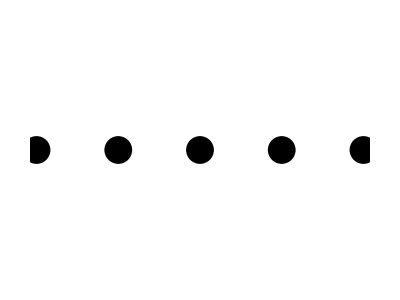

2

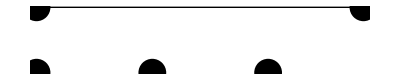

3

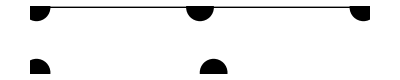

4

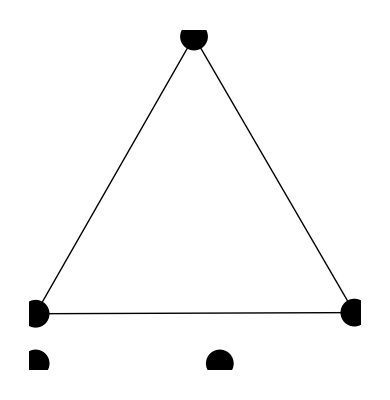

5

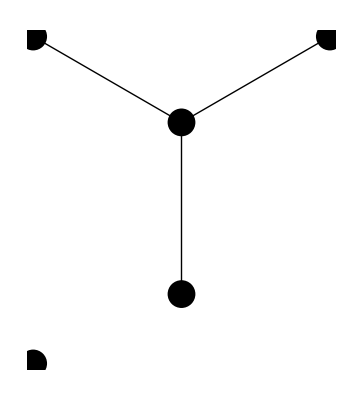

6

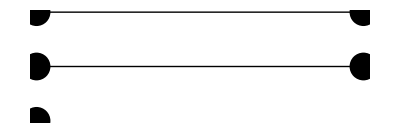

7

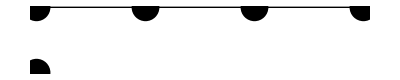

8

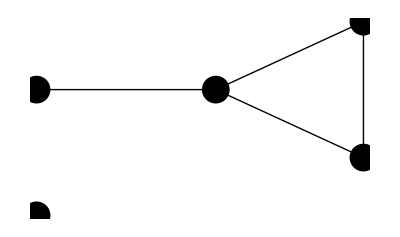

9

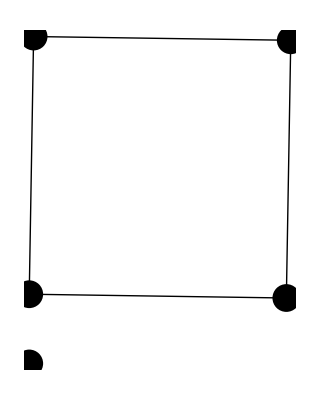

10

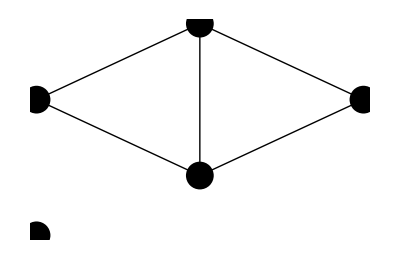

11

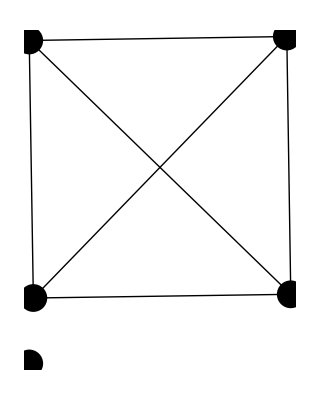

12

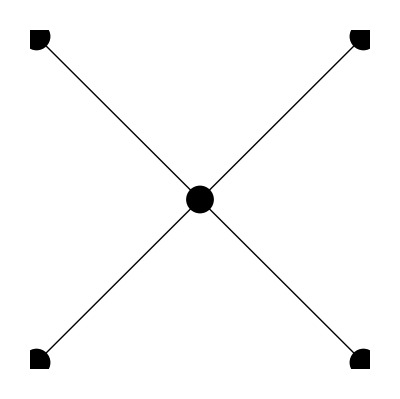

13

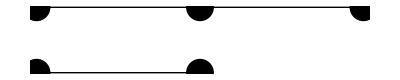

14

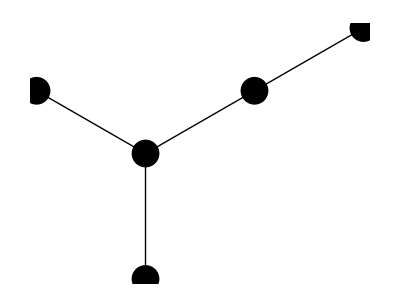

15

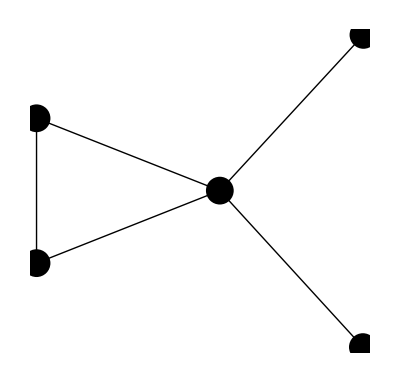

16

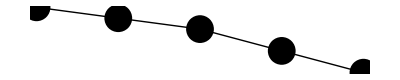

17

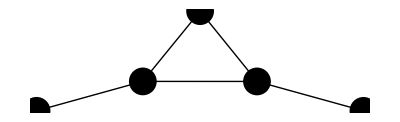

18

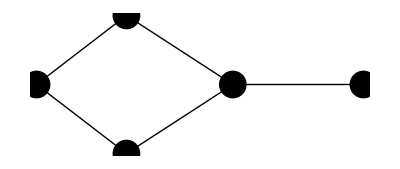

19

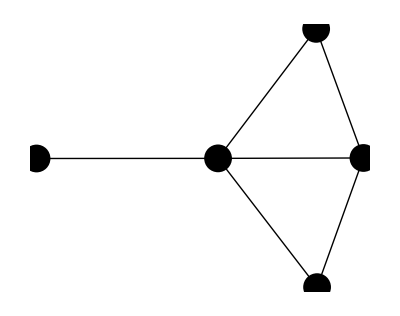

20

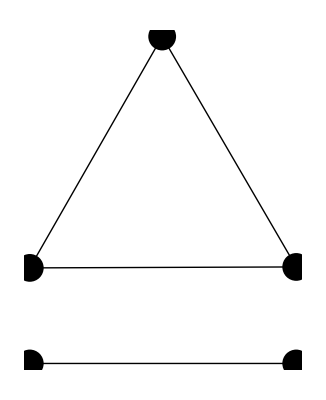

21

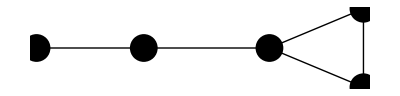

22

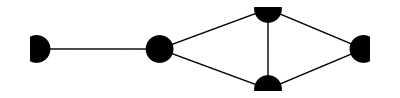

23

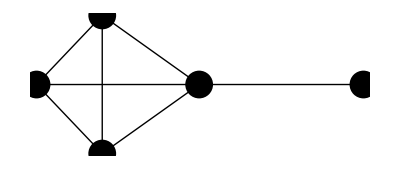

24

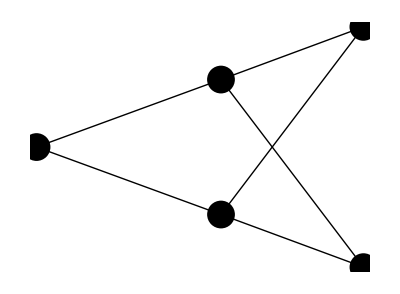

25

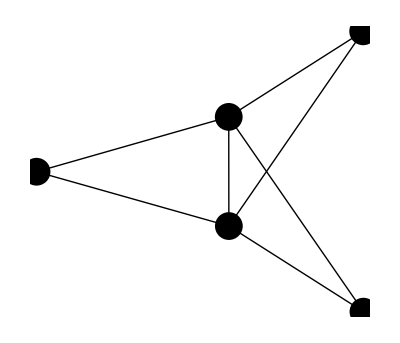

26

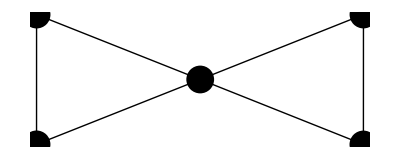

27

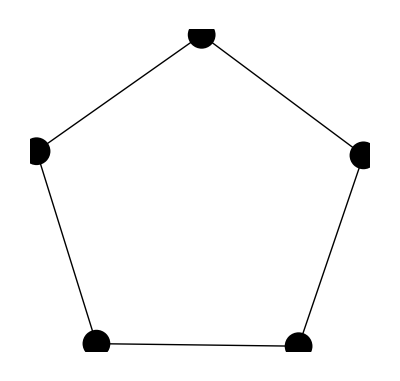

28

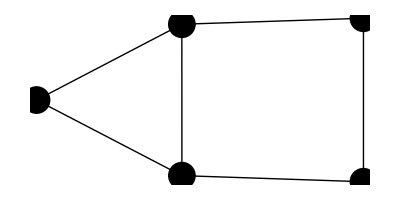

29

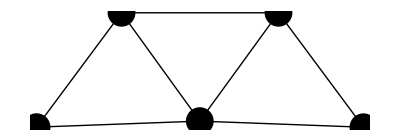

30

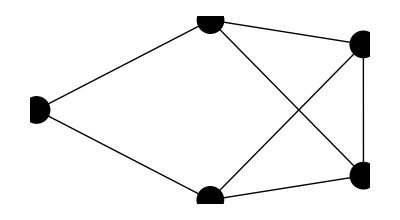

31

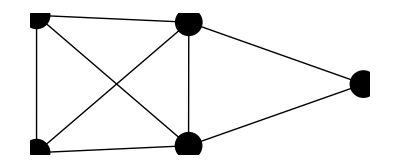

32

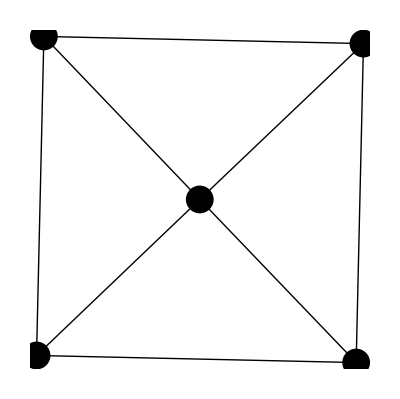

33

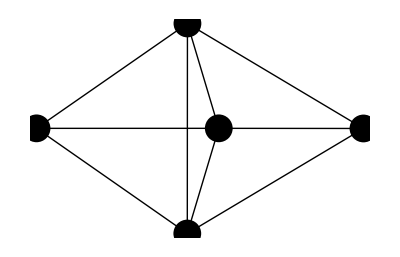

34

-Graphics-

```mathematica
Do[Print[i];
   Print[ GraphPlot[listamatrices2[[i]],PlotStyle->{Black,PointSize[.05]}]];
,{i,Length[listamatrices2]}];
```

```mathematica
<<Combinatorica`
```

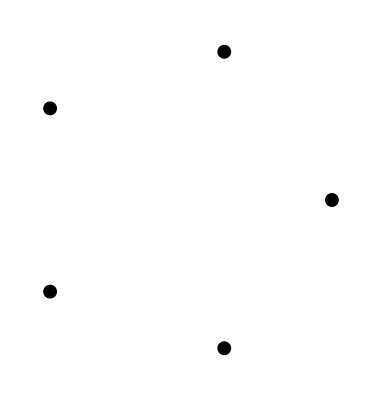
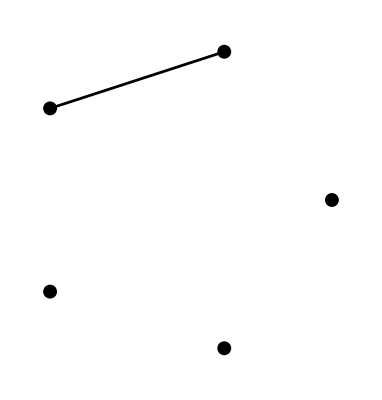
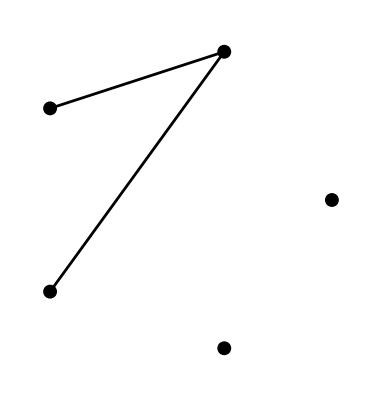
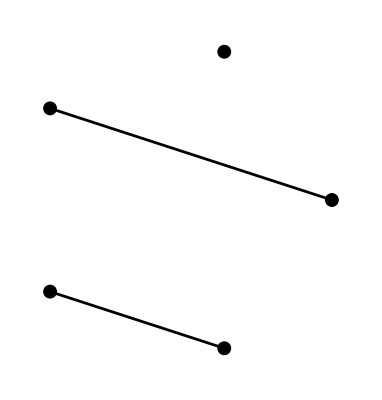
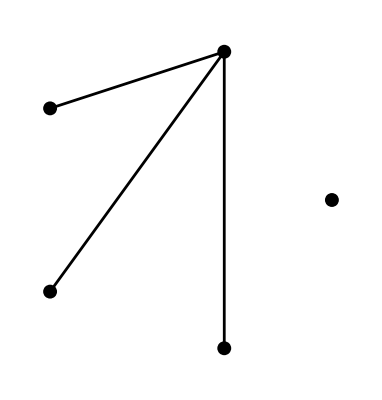
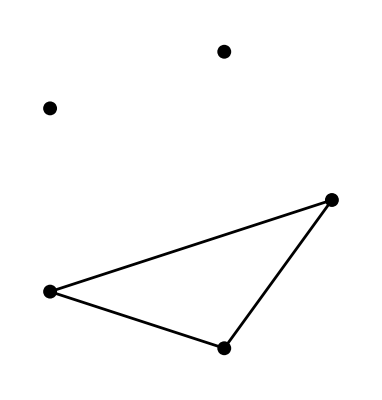
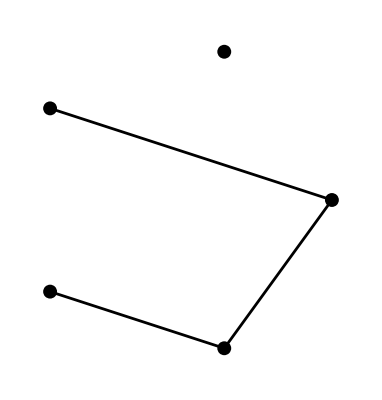
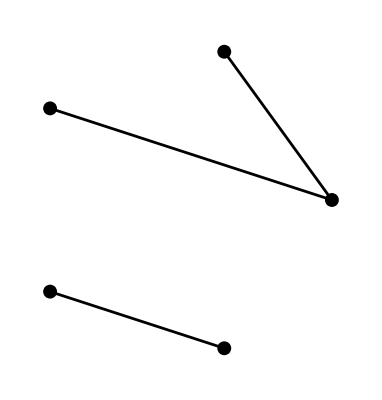
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
ShowGraphArray[ListGraphs[5]]
```

#### Ejemplo 5.17.

```mathematica
n=7;
comb=n*(n-1)/2;
listamatrices=Table[0,{indice,2^comb},{k1,n},{k2,n}];
Do[lista=IntegerDigits[i-1,2];
Do[PrependTo[lista,0];,{f,comb-Length[lista]}];
gg=1;
Do[
Do[
If[lista[[gg]]==1,listamatrices[[i,k2,k1]]=1];
gg++;
,{k1,k2+1,n}];,{k2,n-1}];
listamatrices[[i]]=listamatrices[[i]]+Transpose[listamatrices[[i]]];
,{i,2^comb}];
Print["FIN"];
MemoryInUse[]
```

FIN

1640968184

```mathematica
Timing[ListGraphs[7]]
```

{515.907,{⁃Graph:<0,7,Undirected>⁃,⁃Graph:<1,7,Undirected>⁃,⁃Graph:<2,7,Undirected>⁃,⁃Graph:<2,7,Undirected>⁃,⁃Graph:<3,7,Undirected>⁃,⁃Graph:<3,7,Undirected>⁃,⁃Graph:<3,7,Undirected>⁃,⁃Graph:<3,7,Undirected>⁃,⁃Graph:<3,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<4,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<5,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<6,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<7,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<8,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<9,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<10,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<11,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<12,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<13,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<14,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<15,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<16,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<17,7,Undirected>⁃,⁃Graph:<18,7,Undirected>⁃,⁃Graph:<18,7,Undirected>⁃,⁃Graph:<18,7,Undirected>⁃,⁃Graph:<18,7,Undirected>⁃,⁃Graph:<18,7,Undirected>⁃,⁃Graph:<19,7,Undirected>⁃,⁃Graph:<19,7,Undirected>⁃,⁃Graph:<20,7,Undirected>⁃,⁃Graph:<21,7,Undirected>⁃}}

### 5.2. GRAFOS DE n VÉRTICES y m LADOS

#### Programa 5.13. Grafos de n vértices y m lados

n=NÚMERO DE VÉRTICES;
m=NÚMERO DE LADOS;

comb=(n*(n-1))/2;
numeromatrices=comb!/((comb-m)!*m!);
listamatrices=Table[0,{indice,numeromatrices},{k1,n},{k2,n}];
kc=1;
Do[lista=IntegerDigits[i-1,2];
    If[Sum[lista[[j]],{j,Length[lista]}]==m,
      matriztemp=Table[0,{k1,n},{k2,n}];
      Do[PrependTo[lista,0];,{f,comb-Length[lista]}];
      gg=1;
      Do[
        Do[
            If[lista[[gg]]==1,matriztemp[[k2,k1]]=1];
            gg++;
            ,{k1,k2+1,n}];,{k2,n-1}];
      listamatrices[[kc]]=matriztemp+Transpose[matriztemp];
      kc++;
      ];
    ,{i,2^comb}];
Print["N.ba de matrices: ",Length[listamatrices]];

#### Ejemplo 5.18.

```mathematica
n=6;
m=8;

comb=(n*(n-1))/2;
numeromatrices=comb!/((comb-m)!*m!);
listamatrices=Table[0,{indice,numeromatrices},{k1,n},{k2,n}];
kc=1;
Do[lista=IntegerDigits[i-1,2];
If[Sum[lista[[j]],{j,Length[lista]}]==m,
matriztemp=Table[0,{k1,n},{k2,n}];
Do[PrependTo[lista,0];,{f,comb-Length[lista]}];
gg=1;
Do[
Do[
If[lista[[gg]]==1,matriztemp[[k2,k1]]=1];
gg++;
,{k1,k2+1,n}];,{k2,n-1}];
listamatrices[[kc]]=matriztemp+Transpose[matriztemp];
kc++;
];
,{i,2^comb}];
Print["N.ba de matrices: ",Length[listamatrices]];
```

N.ba de matrices: 6435

```mathematica
ISOMORFAS[A_]:=Module[{j,matricesP},
isomorfas={};
matricesP=Permutations[IdentityMatrix[Dimensions[A][[1]]]];
Do[
isomorfas=Union[isomorfas,{matricesP[[j]].A.Transpose[matricesP[[j]]]}];
,{j,Length[matricesP]}];
isomorfas
];
```

```mathematica
listamatrices2={};
While[listamatrices≠{},
AppendTo[listamatrices2,listamatrices[[1]]];
listamatrices=Complement[listamatrices,ISOMORFAS[listamatrices[[1]]]];
];
Length[listamatrices2]
```

24

```mathematica
<<"GraphUtilities`";
```

1

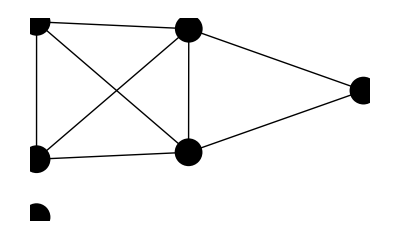

2

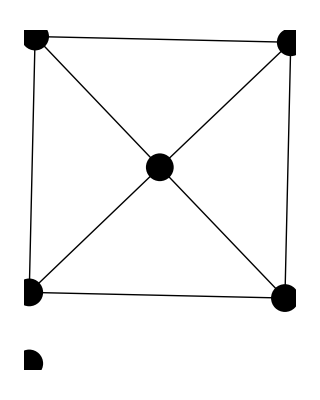

3

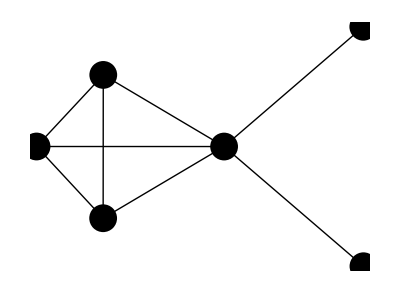

4

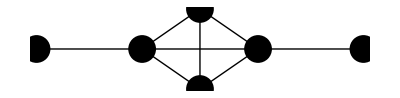

5

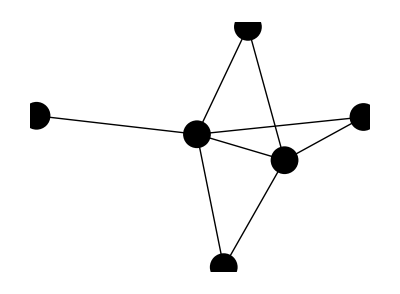

6

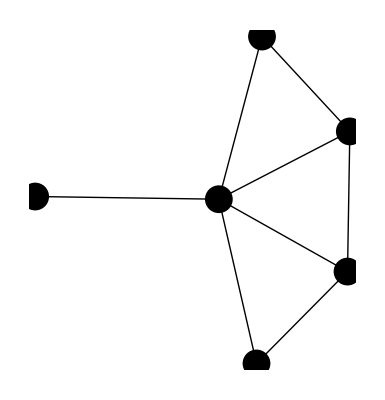

7

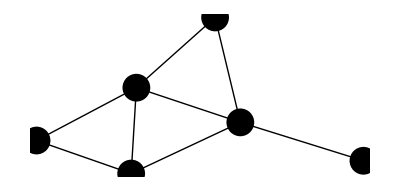

8

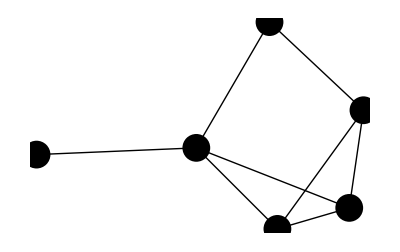

9

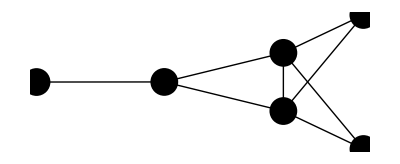

10

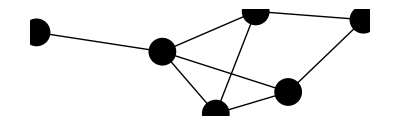

11

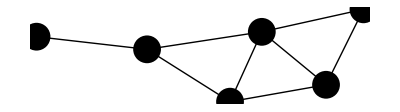

12

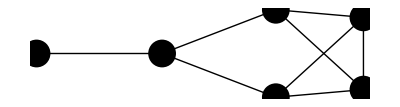

13

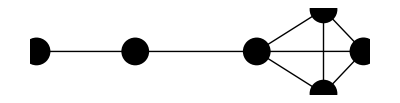

14

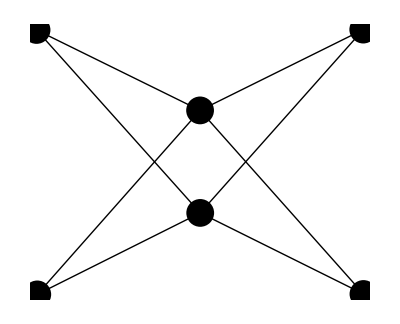

15

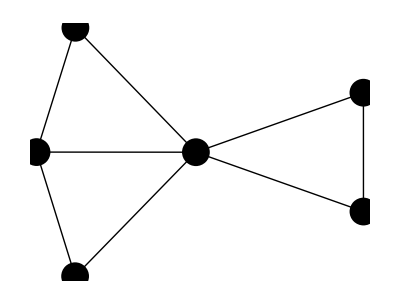

16

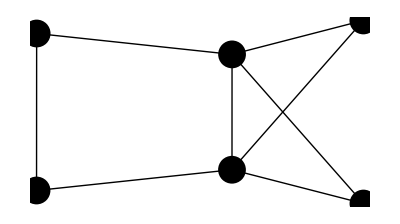

17

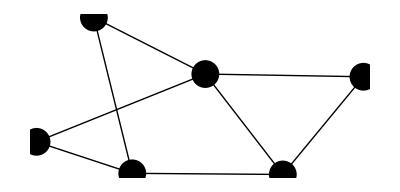

18

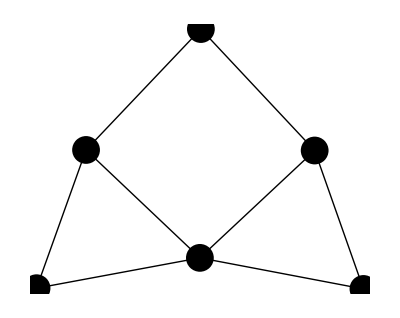

19

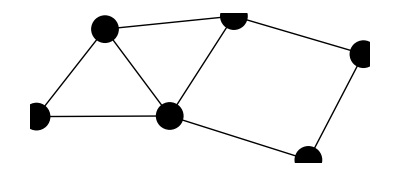

20

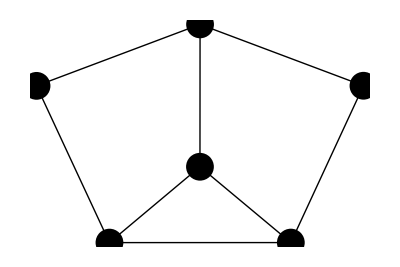

21

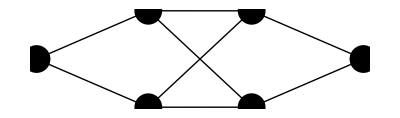

22

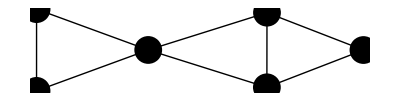

23

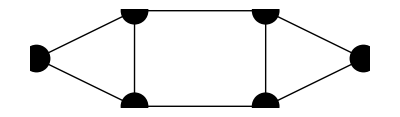

24

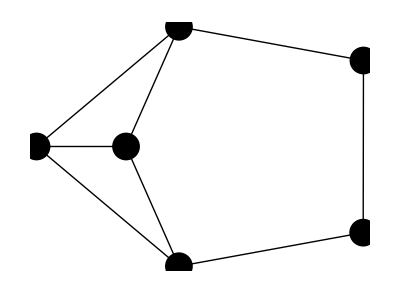

```mathematica
Do[Print[i];
   Print[ GraphPlot[listamatrices2[[i]],PlotStyle->{Black,PointSize[.05]}]];
,{i,Length[listamatrices2]}];
```

```mathematica
<<Combinatorica`
```

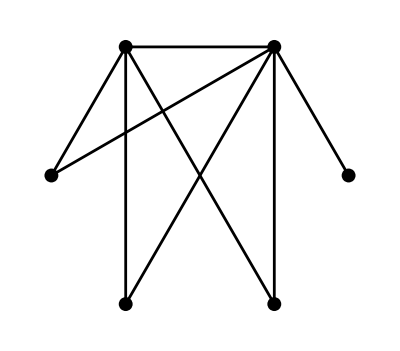
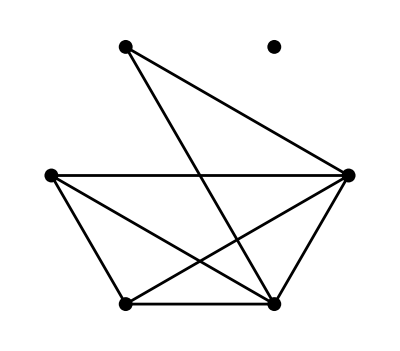
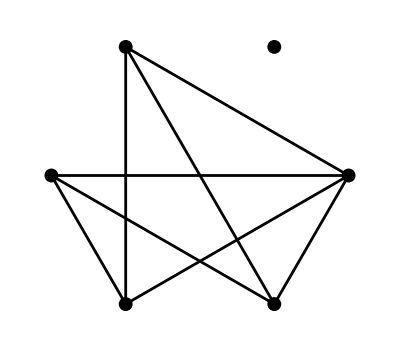
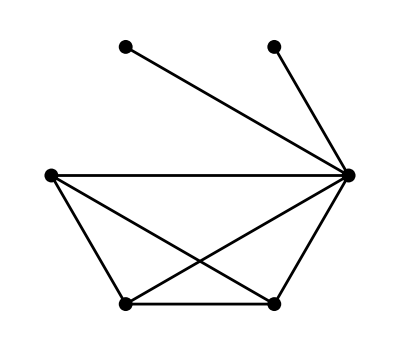
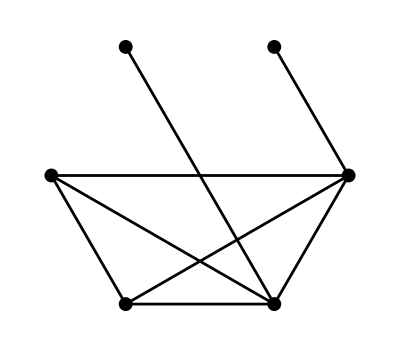
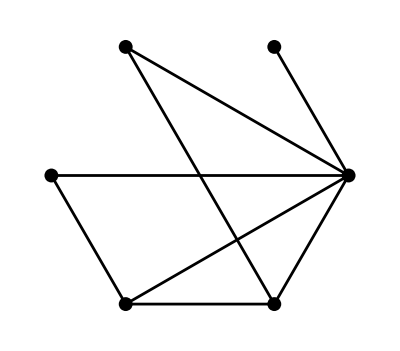
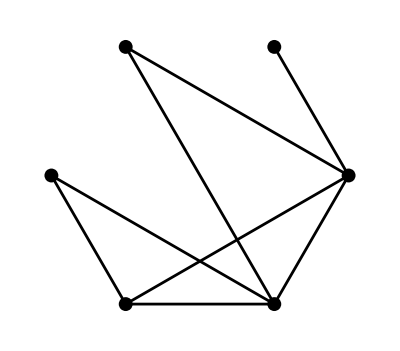
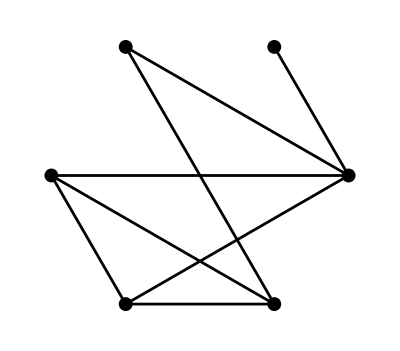

```mathematica
ShowGraphArray[ListGraph[6,8]]
```

### 5.3. GRAFOS QUE CONTIENEN A UNO DADO

#### Función 5.14. Añadirlado[]

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

#### Ejemplo 5.19.

```mathematica
matrizadyacencia={{0,1,0,0,0},{1,0,1,0,1},{0,1,0,1,0},{0,0,1,0,0},{0,1,0,0,0}};
```

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
Añadirlado[matrizadyacencia]
```

{{{0,1,1,0,0},{1,0,1,0,1},{1,1,0,1,0},{0,0,1,0,0},{0,1,0,0,0}},{{0,1,0,1,0},{1,0,1,0,1},{0,1,0,1,0},{1,0,1,0,0},{0,1,0,0,0}},{{0,1,0,0,0},{1,0,1,1,1},{0,1,0,1,0},{0,1,1,0,0},{0,1,0,0,0}},{{0,1,0,0,1},{1,0,1,0,1},{0,1,0,1,0},{0,0,1,0,0},{1,1,0,0,0}},{{0,1,0,0,0},{1,0,1,0,1},{0,1,0,1,1},{0,0,1,0,0},{0,1,1,0,0}},{{0,1,0,0,0},{1,0,1,0,1},{0,1,0,1,0},{0,0,1,0,1},{0,1,0,1,0}}}

```mathematica
listamatrices2={};
While[listamatrices≠{},
AppendTo[listamatrices2,listamatrices[[1]]];
listamatrices=Complement[listamatrices,ISOMORFAS[listamatrices[[1]]]];
];
Length[listamatrices2]
```

4

```mathematica
<<"GraphUtilities`";
```

```mathematica
GraphPlot[matrizadyacencia,PlotStyle->{Black,PointSize[.05]}]
```

-Graphics-

```mathematica
Do[Print[i];
   Print[ GraphPlot[listamatrices2[[i]],PlotStyle->{Black,PointSize[.05]}]];
,{i,Length[listamatrices2]}];
```

1

-Graphics-

2

-Graphics-

3

-Graphics-

4

-Graphics-

#### Programa 5.15. Grafos que contienen a uno dado con un número máximo de lados

ISOMORFAS[A_]:=FUNCIÓN 5.9.;
Añadirlado[matrizadyacencia]:=FUNCIÓN 5.14.;
nlados=NÚMERO DE LADOS A AÑADIR;
matrizadyacencia=MATRIZ DE ADYACENCIA;
n=Dimensions[matrizdeadyacencia][[1]];(NÚMERO DE VÉRTICES)

tiempo=TimeUsed[];
matricesP=Permutations[IdentityMatrix[n]];
Identidad=IdentityMatrix[n];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[
    listamatrices3={};
    
    Do[
      listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
      ,{k2,Length[listamatrices2]}];
    Print["De ",k," lados: ",Length[listamatrices3]];
    
    listamatrices2={};
    While[listamatrices3≠{},
      AppendTo[listamatrices2,listamatrices3[[1]]];
      listamatrices3=Complement[listamatrices3,ISOMORFAS[listamatrices3[[1]]]];
      ];
    
    listamatrices1=Join[listamatrices1,listamatrices2];
    Print["Quedan : ",Length[listamatrices2],". Total: ",Length[listamatrices1]];
    
    ,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];

#### Ejemplo 5.20.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
ISOMORFAS[A_]:=Module[{j,matricesP},
isomorfas={};
matricesP=Permutations[IdentityMatrix[Dimensions[A][[1]]]];
Do[
isomorfas=Union[isomorfas,{matricesP[[j]].A.Transpose[matricesP[[j]]]}];
,{j,Length[matricesP]}];
isomorfas
];
```

```mathematica
nlados=10;
n=5;
matrizadyacencia={{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}};
tiempo=TimeUsed[];
matricesP=Permutations[IdentityMatrix[n]];
Identidad=IdentityMatrix[n];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[
listamatrices3={};

Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
,{k2,Length[listamatrices2]}];
Print["De ",k," lados: ",Length[listamatrices3]];

listamatrices2={};
While[listamatrices3≠{},
AppendTo[listamatrices2,listamatrices3[[1]]];
listamatrices3=Complement[listamatrices3,ISOMORFAS[listamatrices3[[1]]]];
];

listamatrices1=Join[listamatrices1,listamatrices2];
Print["Quedan : ",Length[listamatrices2],". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

De 1 lados: 5

Quedan : 1. Total: 2

De 2 lados: 4

Quedan : 2. Total: 4

De 3 lados: 5

Quedan : 2. Total: 6

De 4 lados: 3

Quedan : 1. Total: 7

De 5 lados: 1

Quedan : 1. Total: 8

De 6 lados: 0

Quedan : 0. Total: 8

De 7 lados: 0

Quedan : 0. Total: 8

De 8 lados: 0

Quedan : 0. Total: 8

De 9 lados: 0

Quedan : 0. Total: 8

De 10 lados: 0

Quedan : 0. Total: 8

Totales: 8 Tiempo empleado: 0.032

```mathematica
<<"GraphUtilities`";
```

```mathematica
Do[Print[i];
   Print[ GraphPlot[listamatrices1[[i]],PlotStyle->{Black,PointSize[.05]}]];
,{i,Length[listamatrices1]}];
```

1

-Graphics-

2

-Graphics-

3

-Graphics-

4

-Graphics-

5

-Graphics-

6

-Graphics-

7

-Graphics-

8

-Graphics-

#### Ejemplo 5.21.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
ISOMORFAS[A_]:=Module[{j,matricesP},
isomorfas={};
matricesP=Permutations[IdentityMatrix[Dimensions[A][[1]]]];
Do[
isomorfas=Union[isomorfas,{matricesP[[j]].A.Transpose[matricesP[[j]]]}];
,{j,Length[matricesP]}];
isomorfas
];
```

```mathematica
nlados=5;
n=6;
matrizadyacencia={{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}};
tiempo=TimeUsed[];
matricesP=Permutations[IdentityMatrix[n]];
Identidad=IdentityMatrix[n];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[
listamatrices3={};

Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
,{k2,Length[listamatrices2]}];
Print["De ",k," lados: ",Length[listamatrices3]];

listamatrices2={};
While[listamatrices3≠{},
AppendTo[listamatrices2,listamatrices3[[1]]];
listamatrices3=Complement[listamatrices3,ISOMORFAS[listamatrices3[[1]]]];
];

listamatrices1=Join[listamatrices1,listamatrices2];
Print["Quedan : ",Length[listamatrices2],". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

De 1 lados: 9

Quedan : 2. Total: 3

De 2 lados: 15

Quedan : 6. Total: 9

De 3 lados: 31

Quedan : 11. Total: 20

De 4 lados: 46

Quedan : 11. Total: 31

De 5 lados: 36

Quedan : 8. Total: 39

Totales: 39 Tiempo empleado: 3.954

```mathematica
<<"GraphUtilities`";
```

```mathematica
Do[Print[i];
   Print[ GraphPlot[listamatrices2[[i]],PlotStyle->{Black,PointSize[.05]}]];
,{i,Length[listamatrices2]}];
```

1

-Graphics-

2

-Graphics-

3

-Graphics-

4

-Graphics-

5

-Graphics-

6

-Graphics-

7

-Graphics-

8

-Graphics-

```mathematica
nlados=5;
n=6;
matrizadyacencia={{0,1,0,0,1,0},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{1,0,0,1,0,0},{0,0,0,0,0,0}};
tiempo=TimeUsed[];
matricesP=Permutations[IdentityMatrix[n]];
Identidad=IdentityMatrix[n];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[
listamatrices3={};

Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
,{k2,Length[listamatrices2]}];
Print["De ",k," lados: ",Length[listamatrices3]];

listamatrices2={};
While[listamatrices3≠{},
AppendTo[listamatrices2,listamatrices3[[1]]];
listamatrices3=Complement[listamatrices3,ISOMORFAS[listamatrices3[[1]]]];
];

listamatrices1=Join[listamatrices1,listamatrices2];
Print["Quedan : ",Length[listamatrices2],". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

De 1 lados: 10

Quedan : 2. Total: 3

De 2 lados: 17

Quedan : 7. Total: 10

De 3 lados: 43

Quedan : 15. Total: 25

De 4 lados: 72

Quedan : 18. Total: 43

De 5 lados: 75

Quedan : 15. Total: 58

Totales: 58 Tiempo empleado: 6.359

```mathematica
Do[Print[i];
   Print[ GraphPlot[listamatrices2[[i]],PlotStyle->{Black,PointSize[.05]}]];
,{i,Length[listamatrices2]}];
```

1

-Graphics-

2

-Graphics-

3

-Graphics-

4

-Graphics-

5

-Graphics-

6

-Graphics-

7

-Graphics-

8

-Graphics-

9

-Graphics-

10

-Graphics-

11

-Graphics-

12

-Graphics-

13

-Graphics-

14

-Graphics-

15

-Graphics-

#### Ejemplo 5.22.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
ISOMORFAS[A_]:=Module[{j,matricesP},
isomorfas={};
matricesP=Permutations[IdentityMatrix[Dimensions[A][[1]]]];
Do[
isomorfas=Union[isomorfas,{matricesP[[j]].A.Transpose[matricesP[[j]]]}];
,{j,Length[matricesP]}];
isomorfas
];
```

```mathematica
n=5;
nlados=n*(n-1)/2;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
matricesP=Permutations[IdentityMatrix[n]];
Identidad=IdentityMatrix[n];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[
listamatrices3={};

Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
,{k2,Length[listamatrices2]}];
Print["De ",k," lados: ",Length[listamatrices3]];

listamatrices2={};
While[listamatrices3≠{},
AppendTo[listamatrices2,listamatrices3[[1]]];
listamatrices3=Complement[listamatrices3,ISOMORFAS[listamatrices3[[1]]]];
];

listamatrices1=Join[listamatrices1,listamatrices2];
Print["Quedan : ",Length[listamatrices2],". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

De 1 lados: 10

Quedan : 1. Total: 2

De 2 lados: 9

Quedan : 2. Total: 4

De 3 lados: 15

Quedan : 4. Total: 8

De 4 lados: 25

Quedan : 6. Total: 14

De 5 lados: 32

Quedan : 6. Total: 20

De 6 lados: 23

Quedan : 6. Total: 26

De 7 lados: 19

Quedan : 4. Total: 30

De 8 lados: 9

Quedan : 2. Total: 32

De 9 lados: 3

Quedan : 1. Total: 33

De 10 lados: 1

Quedan : 1. Total: 34

Totales: 34 Tiempo empleado: 0.203

### 5.4. EFICACIA Y OPTIMIZACIÓN

#### 5.4.1. NO DISPONEMOS DE UNA CONDICIÓN SUFICIENTE

#### Función 5.16. ISOMORFOSPARTE2[]

```mathematica
ISOMORFOSPARTE2[A1_,A2_,tabla1_,tabla2_]:=Module[{n,permutaciones2,adyacentes1,condicion,imagenes,i,j,k,h,kk,permutaciones},
sonisomorfos=False;
n=Dimensions[A1][[1]];
permutaciones=Position[tabla2,tabla1[[1]]];
Do[
permutaciones2={};
adyacentes1=Position[A1[[i]],1];
Do[
imagenes=Complement[Position[tabla2,tabla1[[i]]],Table[{permutaciones[[j]][[kk]]},{kk,Length[permutaciones[[j]]]}]];
Do[
condicion=True;
Do[
If[adyacentes1[[k]][[1]]<i,
If[A2[[permutaciones[[j]][[adyacentes1[[k]][[1]]]],imagenes[[h]][[1]]]]!=1,condicion=False;Break[];];
];
,{k,Length[adyacentes1]}];
If[condicion,
permutaciones2=Join[permutaciones2,{Join[permutaciones[[j]],{imagenes[[h]][[1]]}]}];
If[i==n,sonisomorfos=True;Break[];];
];
,{h,Length[imagenes]}];
If[Mod[j,1000]==0,Print["Van ",j,",  ",Length[permutaciones2]];];
If[sonisomorfos,Break[];];
,{j,Length[permutaciones]}];
permutaciones=permutaciones2;
,{i,2,n}];
sonisomorfos];
```

#### Función 5.17. QUITARISOMORFOS[]

```mathematica
QUITARISOMORFOS[listamatrices_]:=Module[{i,i1,i2,invariantes,potencias,posiciones,kk,j,invariantesordenados,n,tabla,posiblesisomorfos,clase,listamat,isomorfos,k3},

invariantes={};
invariantesordenados={};
posiblesisomorfos={};
n=Dimensions[listamatrices[[1]]][[1]];
potencias=3;
Do[
tabla=Table[Table[MatrixPower[listamatrices[[i]],kk+1][[j,j]],{kk,potencias}],{j,n}];
AppendTo[invariantesordenados,Sort[tabla]];
AppendTo[invariantes,tabla];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];

While[posiciones≠{},
clase=Position[invariantesordenados,invariantesordenados[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};

Do[
listamat=Table[{listamatrices[[posiblesisomorfos[[j]][[k1]][[1]]]],invariantes[[posiblesisomorfos[[j]][[k1]][[1]]]]},{k1,Length[posiblesisomorfos[[j]]]}];

If[Length[listamat]==1,
AppendTo[listamat2,listamat[[1]][[1]]];
,

kk=0;
While[listamat≠{},
AppendTo[listamat2,listamat[[1]][[1]]];
kk++;
isomorfos={};
If[Length[listamat]>1,
Do[

If[ISOMORFOSPARTE2[listamat[[1]][[1]],listamat[[k3]][[1]],listamat[[1]][[2]],listamat[[k3]][[2]]],
AppendTo[isomorfos,{k3}];
];

,{k3,2,Length[listamat]}];
];
listamat=Delete[listamat,Union[{{1}},isomorfos]];
];
If[kk≠1,
Print["En la clase ", j, " hay ",kk, " que no son isomorfos"];
];
];
,{j,Length[posiblesisomorfos]}];
listamat2
];
```

#### Programa 5.18. Combinatoria en grafos

ISOMORFAS[A_]:=FUNCIÓN 5.9;
Añadirlado[matrizadyacencia]:=FUNCIÓN 5.14.;
ISOMORFOSPARTE2[A1_,A2_,tabla1_,tabla2_]:=FUNCIÓN 5.16.;
QUITARISOMORFOS[listamatrices_]:=FUNCIÓN 5.17.;
nlados=NÚMERO DE LADOS;
n=NÚMERO DE VÉRTICES;
matrizadyacencia=MATRIZ DE ADYACENCIA;

tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[
    
    listamatrices3={};
    Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
    Do[
      listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
      If[Mod[k2,100]==1,Print["Van ",k2];];
      ,{k2,Length[listamatrices2]}];
    Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];
    
    listamatrices2=QUITARISOMORFOS[listamatrices3];
    
    listamatrices1=Join[listamatrices1,listamatrices2];
    Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];
    
    ,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];

#### Ejemplo 5.23.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
ISOMORFOSPARTE2[A1_,A2_,tabla1_,tabla2_]:=Module[{potencias,n,permutaciones2,adyacentes1,condicion,imagenes,i,j,k,h,kk,permutaciones},
potencias=3;
sonisomorfos=False;
n=Dimensions[A1][[1]];
permutaciones=Position[tabla2,tabla1[[1]]];
Do[
permutaciones2={};
adyacentes1=Position[A1[[i]],1];
Do[
imagenes=Complement[Position[tabla2,tabla1[[i]]],Table[{permutaciones[[j]][[kk]]},{kk,Length[permutaciones[[j]]]}]];
Do[
condicion=True;
Do[
If[adyacentes1[[k]][[1]]<i,
If[A2[[permutaciones[[j]][[adyacentes1[[k]][[1]]]],imagenes[[h]][[1]]]]!=1,condicion=False;Break[];];
];
,{k,Length[adyacentes1]}];
If[condicion,
permutaciones2=Join[permutaciones2,{Join[permutaciones[[j]],{imagenes[[h]][[1]]}]}];
If[i==n,sonisomorfos=True;Break[];];
];
,{h,Length[imagenes]}];
If[Mod[j,1000]==0,Print["Van ",j,",  ",Length[permutaciones2]];];
If[sonisomorfos,Break[];];
,{j,Length[permutaciones]}];
permutaciones=permutaciones2;
,{i,2,n}];
sonisomorfos];
```

```mathematica
QUITARISOMORFOS[listamatrices_]:=Module[{i,i1,i2,invariantes,potencias,posiciones,kk,j,invariantesordenados,n,tabla,posiblesisomorfos,clase,listamat,isomorfos,k3},

invariantes={};
invariantesordenados={};
posiblesisomorfos={};
n=Dimensions[listamatrices[[1]]][[1]];
potencias=3;
Do[
tabla=Table[Table[MatrixPower[listamatrices[[i]],kk+1][[j,j]],{kk,potencias}],{j,n}];
AppendTo[invariantesordenados,Sort[tabla]];
AppendTo[invariantes,tabla];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];

While[posiciones≠{},
clase=Position[invariantesordenados,invariantesordenados[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};

Do[
listamat=Table[{listamatrices[[posiblesisomorfos[[j]][[k1]][[1]]]],invariantes[[posiblesisomorfos[[j]][[k1]][[1]]]]},{k1,Length[posiblesisomorfos[[j]]]}];

If[Length[listamat]==1,
AppendTo[listamat2,listamat[[1]][[1]]];
,

kk=0;
While[listamat≠{},
AppendTo[listamat2,listamat[[1]][[1]]];
kk++;
isomorfos={};
If[Length[listamat]>1,
Do[

If[ISOMORFOSPARTE2[listamat[[1]][[1]],listamat[[k3]][[1]],listamat[[1]][[2]],listamat[[k3]][[2]]],
AppendTo[isomorfos,{k3}];
];

,{k3,2,Length[listamat]}];
];
listamat=Delete[listamat,Union[{{1}},isomorfos]];
];
If[kk≠1,
Print["En la clase ", j, " hay ",kk, " que no son isomorfos"];
];
];
,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
n=7;
nlados=(n*(n-1))/2;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 21 *************

DIVIDIMOS EN 1 CLASES

0.797. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 20 *************

DIVIDIMOS EN 2 CLASES

1.062. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 37 *************

DIVIDIMOS EN 5 CLASES

1.297. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 86 *************

DIVIDIMOS EN 10 CLASES

1.766. Total: 19

-------> Añadimos nuevo lado a 10 grafos

Van 1

************* DE 5 LADOS: 157 *************

DIVIDIMOS EN 21 CLASES

2.562. Total: 40

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 6 LADOS: 306 *************

DIVIDIMOS EN 41 CLASES

3.984. Total: 81

-------> Añadimos nuevo lado a 41 grafos

Van 1

************* DE 7 LADOS: 533 *************

DIVIDIMOS EN 65 CLASES

6.516. Total: 146

-------> Añadimos nuevo lado a 65 grafos

Van 1

************* DE 8 LADOS: 759 *************

DIVIDIMOS EN 97 CLASES

9.922. Total: 243

-------> Añadimos nuevo lado a 97 grafos

Van 1

************* DE 9 LADOS: 1033 *************

DIVIDIMOS EN 131 CLASES

14.766. Total: 374

-------> Añadimos nuevo lado a 131 grafos

Van 1

Van 101

************* DE 10 LADOS: 1271 *************

DIVIDIMOS EN 148 CLASES

21.. Total: 522

-------> Añadimos nuevo lado a 148 grafos

Van 1

Van 101

************* DE 11 LADOS: 1293 *************

DIVIDIMOS EN 148 CLASES

27.562. Total: 670

-------> Añadimos nuevo lado a 148 grafos

Van 1

Van 101

************* DE 12 LADOS: 1152 *************

DIVIDIMOS EN 131 CLASES

33.453. Total: 801

-------> Añadimos nuevo lado a 131 grafos

Van 1

Van 101

************* DE 13 LADOS: 900 *************

DIVIDIMOS EN 97 CLASES

38.078. Total: 898

-------> Añadimos nuevo lado a 97 grafos

Van 1

************* DE 14 LADOS: 591 *************

DIVIDIMOS EN 65 CLASES

41.094. Total: 963

-------> Añadimos nuevo lado a 65 grafos

Van 1

************* DE 15 LADOS: 339 *************

DIVIDIMOS EN 41 CLASES

42.953. Total: 1004

-------> Añadimos nuevo lado a 41 grafos

Van 1

************* DE 16 LADOS: 182 *************

DIVIDIMOS EN 21 CLASES

44.328. Total: 1025

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 17 LADOS: 79 *************

DIVIDIMOS EN 10 CLASES

45.031. Total: 1035

-------> Añadimos nuevo lado a 10 grafos

Van 1

************* DE 18 LADOS: 30 *************

DIVIDIMOS EN 5 CLASES

45.437. Total: 1040

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 19 LADOS: 11 *************

DIVIDIMOS EN 2 CLASES

45.703. Total: 1042

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 20 LADOS: 3 *************

DIVIDIMOS EN 1 CLASES

45.844. Total: 1043

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 21 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

45.859. Total: 1044

Totales: 1044 Tiempo empleado: 45.859

#### Ejemplo 5.24.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
ISOMORFOSPARTE2[A1_,A2_,tabla1_,tabla2_]:=Module[{n,permutaciones2,adyacentes1,condicion,imagenes,i,j,k,h,kk,permutaciones},
sonisomorfos=False;
n=Dimensions[A1][[1]];
permutaciones=Position[tabla2,tabla1[[1]]];
Do[
permutaciones2={};
adyacentes1=Position[A1[[i]],1];
Do[
imagenes=Complement[Position[tabla2,tabla1[[i]]],Table[{permutaciones[[j]][[kk]]},{kk,Length[permutaciones[[j]]]}]];
Do[
condicion=True;
Do[
If[adyacentes1[[k]][[1]]<i,
If[A2[[permutaciones[[j]][[adyacentes1[[k]][[1]]]],imagenes[[h]][[1]]]]!=1,condicion=False;Break[];];
];
,{k,Length[adyacentes1]}];
If[condicion,
permutaciones2=Join[permutaciones2,{Join[permutaciones[[j]],{imagenes[[h]][[1]]}]}];
If[i==n,sonisomorfos=True;Break[];];
];
,{h,Length[imagenes]}];
If[Mod[j,1000]==0,Print["Van ",j,",  ",Length[permutaciones2]];];
If[sonisomorfos,Break[];];
,{j,Length[permutaciones]}];
permutaciones=permutaciones2;
,{i,2,n}];
sonisomorfos];
```

```mathematica
QUITARISOMORFOS[listamatrices_]:=Module[{i,i1,i2,invariantes,potencias,posiciones,kk,j,invariantesordenados,n,tabla,posiblesisomorfos,clase,listamat,isomorfos,k3},

invariantes={};
invariantesordenados={};
posiblesisomorfos={};
n=Dimensions[listamatrices[[1]]][[1]];
potencias=3;
Do[
tabla=Table[Table[MatrixPower[listamatrices[[i]],kk+1][[j,j]],{kk,potencias}],{j,n}];
AppendTo[invariantesordenados,Sort[tabla]];
AppendTo[invariantes,tabla];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];

While[posiciones≠{},
clase=Position[invariantesordenados,invariantesordenados[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};

Do[
listamat=Table[{listamatrices[[posiblesisomorfos[[j]][[k1]][[1]]]],invariantes[[posiblesisomorfos[[j]][[k1]][[1]]]]},{k1,Length[posiblesisomorfos[[j]]]}];

If[Length[listamat]==1,
AppendTo[listamat2,listamat[[1]][[1]]];
,

kk=0;
While[listamat≠{},
AppendTo[listamat2,listamat[[1]][[1]]];
kk++;
isomorfos={};
If[Length[listamat]>1,
Do[

If[ISOMORFOSPARTE2[listamat[[1]][[1]],listamat[[k3]][[1]],listamat[[1]][[2]],listamat[[k3]][[2]]],
AppendTo[isomorfos,{k3}];
];

,{k3,2,Length[listamat]}];
];
listamat=Delete[listamat,Union[{{1}},isomorfos]];
];
If[kk≠1,
Print["En la clase ", j, " hay ",kk, " que no son isomorfos"];
];
];
,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
n=9;
nlados=2;
matrizadyacencia={{0,1,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,0,1,0,1,0,0,0,0},{0,0,0,1,0,1,0,0,0},{0,0,0,0,1,0,1,0,0},{0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,1,0}};
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 27 *************

DIVIDIMOS EN 3 CLASES

0.219. Total: 4

-------> Añadimos nuevo lado a 3 grafos

Van 1

************* DE 2 LADOS: 75 *************

DIVIDIMOS EN 27 CLASES

0.656. Total: 31

Totales: 31 Tiempo empleado: 0.656

```mathematica
<<"GraphUtilities`";
```

```mathematica
Do[Print[i];
   Print[ GraphPlot[listamatrices2[[i]],PlotStyle->{Black,PointSize[.05]}]];
,{i,Length[listamatrices2]}];
```

1

-Graphics-

2

-Graphics-

3

-Graphics-

4

-Graphics-

5

-Graphics-

6

-Graphics-

7

-Graphics-

8

-Graphics-

9

-Graphics-

10

-Graphics-

11

-Graphics-

12

-Graphics-

13

-Graphics-

14

-Graphics-

15

-Graphics-

16

-Graphics-

17

-Graphics-

18

-Graphics-

19

-Graphics-

20

-Graphics-

21

-Graphics-

22

-Graphics-

23

-Graphics-

24

-Graphics-

25

-Graphics-

26

-Graphics-

27

-Graphics-

#### Ejemplo 5.25.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
ISOMORFOSPARTE2[A1_,A2_,tabla1_,tabla2_]:=Module[{n,permutaciones2,adyacentes1,condicion,imagenes,i,j,k,h,kk,permutaciones},
sonisomorfos=False;
n=Dimensions[A1][[1]];
permutaciones=Position[tabla2,tabla1[[1]]];
Do[
permutaciones2={};
adyacentes1=Position[A1[[i]],1];
Do[
imagenes=Complement[Position[tabla2,tabla1[[i]]],Table[{permutaciones[[j]][[kk]]},{kk,Length[permutaciones[[j]]]}]];
Do[
condicion=True;
Do[
If[adyacentes1[[k]][[1]]<i,
If[A2[[permutaciones[[j]][[adyacentes1[[k]][[1]]]],imagenes[[h]][[1]]]]!=1,condicion=False;Break[];];
];
,{k,Length[adyacentes1]}];
If[condicion,
permutaciones2=Join[permutaciones2,{Join[permutaciones[[j]],{imagenes[[h]][[1]]}]}];
If[i==n,sonisomorfos=True;Break[];];
];
,{h,Length[imagenes]}];
If[Mod[j,1000]==0,Print["Van ",j,",  ",Length[permutaciones2]];];
If[sonisomorfos,Break[];];
,{j,Length[permutaciones]}];
permutaciones=permutaciones2;
,{i,2,n}];
sonisomorfos];
```

```mathematica
QUITARISOMORFOS[listamatrices_]:=Module[{i,i1,i2,invariantes,potencias,posiciones,kk,j,invariantesordenados,n,tabla,posiblesisomorfos,clase,listamat,isomorfos,k3},

invariantes={};
invariantesordenados={};
posiblesisomorfos={};
n=Dimensions[listamatrices[[1]]][[1]];
potencias=3;
Do[
tabla=Table[Table[MatrixPower[listamatrices[[i]],kk+1][[j,j]],{kk,potencias}],{j,n}];
AppendTo[invariantesordenados,Sort[tabla]];
AppendTo[invariantes,tabla];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];

While[posiciones≠{},
clase=Position[invariantesordenados,invariantesordenados[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};

Do[
listamat=Table[{listamatrices[[posiblesisomorfos[[j]][[k1]][[1]]]],invariantes[[posiblesisomorfos[[j]][[k1]][[1]]]]},{k1,Length[posiblesisomorfos[[j]]]}];

If[Length[listamat]==1,
AppendTo[listamat2,listamat[[1]][[1]]];
,

kk=0;
While[listamat≠{},
AppendTo[listamat2,listamat[[1]][[1]]];
kk++;
isomorfos={};
If[Length[listamat]>1,
Do[

If[ISOMORFOSPARTE2[listamat[[1]][[1]],listamat[[k3]][[1]],listamat[[1]][[2]],listamat[[k3]][[2]]],
AppendTo[isomorfos,{k3}];
];

,{k3,2,Length[listamat]}];
];
listamat=Delete[listamat,Union[{{1}},isomorfos]];
];
If[kk≠1,
Print["En la clase ", j, " hay ",kk, " que no son isomorfos"];
];
];
,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
nlados=2;
n=12;
matrizadyacencia={{0,1,0,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,0,0,1,0}};
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 54 *************

DIVIDIMOS EN 3 CLASES

En la clase 3 hay 3 que no son isomorfos

0.5. Total: 6

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 2 LADOS: 255 *************

DIVIDIMOS EN 46 CLASES

En la clase 9 hay 4 que no son isomorfos

En la clase 12 hay 2 que no son isomorfos

En la clase 14 hay 3 que no son isomorfos

En la clase 16 hay 5 que no son isomorfos

En la clase 20 hay 3 que no son isomorfos

En la clase 21 hay 3 que no son isomorfos

En la clase 22 hay 2 que no son isomorfos

En la clase 25 hay 4 que no son isomorfos

En la clase 26 hay 3 que no son isomorfos

En la clase 31 hay 2 que no son isomorfos

En la clase 32 hay 5 que no son isomorfos

En la clase 33 hay 5 que no son isomorfos

En la clase 36 hay 2 que no son isomorfos

En la clase 37 hay 2 que no son isomorfos

En la clase 38 hay 2 que no son isomorfos

En la clase 39 hay 2 que no son isomorfos

2.5. Total: 85

Totales: 85 Tiempo empleado: 2.5

```mathematica
QUITARISOMORFOS[listamatrices_]:=Module[{i,i1,i2,invariantes,potencias,posiciones,kk,j,invariantesordenados,n,tabla,posiblesisomorfos,clase,listamat,isomorfos,k3},

invariantes={};
invariantesordenados={};
posiblesisomorfos={};
n=Dimensions[listamatrices[[1]]][[1]];
potencias=5;
Do[
tabla=Table[Table[MatrixPower[listamatrices[[i]],kk+1][[j,j]],{kk,potencias}],{j,n}];
AppendTo[invariantesordenados,Sort[tabla]];
AppendTo[invariantes,tabla];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];

While[posiciones≠{},
clase=Position[invariantesordenados,invariantesordenados[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};

Do[
listamat=Table[{listamatrices[[posiblesisomorfos[[j]][[k1]][[1]]]],invariantes[[posiblesisomorfos[[j]][[k1]][[1]]]]},{k1,Length[posiblesisomorfos[[j]]]}];

If[Length[listamat]==1,
AppendTo[listamat2,listamat[[1]][[1]]];
,

kk=0;
While[listamat≠{},
AppendTo[listamat2,listamat[[1]][[1]]];
kk++;
isomorfos={};
If[Length[listamat]>1,
Do[

If[ISOMORFOSPARTE2[listamat[[1]][[1]],listamat[[k3]][[1]],listamat[[1]][[2]],listamat[[k3]][[2]]],
AppendTo[isomorfos,{k3}];
];

,{k3,2,Length[listamat]}];
];
listamat=Delete[listamat,Union[{{1}},isomorfos]];
];
If[kk≠1,
Print["En la clase ", j, " hay ",kk, " que no son isomorfos"];
];
];
,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
nlados=2;
n=12;
matrizadyacencia={{0,1,0,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,0,0,1,0}};
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 54 *************

DIVIDIMOS EN 5 CLASES

0.688. Total: 6

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 2 LADOS: 255 *************

DIVIDIMOS EN 79 CLASES

3.797. Total: 85

Totales: 85 Tiempo empleado: 3.797

#### 5.4.2. DISPONEMOS DE UNA CONDICIÓN SUFICIENTE

#### Función 5.19. QUITARISOMORFOS2[]

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

#### Ejemplo 5.26.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
n=7;
nlados=(n*(n-1))/2;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 21 *************

DIVIDIMOS EN 1 CLASES

-1.42109×10^-14. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 20 *************

DIVIDIMOS EN 2 CLASES

-1.42109×10^-14. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 37 *************

DIVIDIMOS EN 5 CLASES

-1.42109×10^-14. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 86 *************

DIVIDIMOS EN 10 CLASES

0.015. Total: 19

-------> Añadimos nuevo lado a 10 grafos

Van 1

************* DE 5 LADOS: 157 *************

DIVIDIMOS EN 21 CLASES

0.078. Total: 40

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 6 LADOS: 306 *************

DIVIDIMOS EN 41 CLASES

0.218. Total: 81

-------> Añadimos nuevo lado a 41 grafos

Van 1

************* DE 7 LADOS: 533 *************

DIVIDIMOS EN 65 CLASES

0.609. Total: 146

-------> Añadimos nuevo lado a 65 grafos

Van 1

************* DE 8 LADOS: 759 *************

DIVIDIMOS EN 97 CLASES

1.25. Total: 243

-------> Añadimos nuevo lado a 97 grafos

Van 1

************* DE 9 LADOS: 1033 *************

DIVIDIMOS EN 131 CLASES

2.359. Total: 374

-------> Añadimos nuevo lado a 131 grafos

Van 1

Van 101

************* DE 10 LADOS: 1271 *************

DIVIDIMOS EN 148 CLASES

3.921. Total: 522

-------> Añadimos nuevo lado a 148 grafos

Van 1

Van 101

************* DE 11 LADOS: 1293 *************

DIVIDIMOS EN 148 CLASES

5.578. Total: 670

-------> Añadimos nuevo lado a 148 grafos

Van 1

Van 101

************* DE 12 LADOS: 1152 *************

DIVIDIMOS EN 131 CLASES

7.046. Total: 801

-------> Añadimos nuevo lado a 131 grafos

Van 1

Van 101

************* DE 13 LADOS: 900 *************

DIVIDIMOS EN 97 CLASES

7.937. Total: 898

-------> Añadimos nuevo lado a 97 grafos

Van 1

************* DE 14 LADOS: 591 *************

DIVIDIMOS EN 65 CLASES

8.468. Total: 963

-------> Añadimos nuevo lado a 65 grafos

Van 1

************* DE 15 LADOS: 339 *************

DIVIDIMOS EN 41 CLASES

8.703. Total: 1004

-------> Añadimos nuevo lado a 41 grafos

Van 1

************* DE 16 LADOS: 182 *************

DIVIDIMOS EN 21 CLASES

8.781. Total: 1025

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 17 LADOS: 79 *************

DIVIDIMOS EN 10 CLASES

8.828. Total: 1035

-------> Añadimos nuevo lado a 10 grafos

Van 1

************* DE 18 LADOS: 30 *************

DIVIDIMOS EN 5 CLASES

8.859. Total: 1040

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 19 LADOS: 11 *************

DIVIDIMOS EN 2 CLASES

8.875. Total: 1042

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 20 LADOS: 3 *************

DIVIDIMOS EN 1 CLASES

8.875. Total: 1043

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 21 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

8.875. Total: 1044

Totales: 1044 Tiempo empleado: 8.875

#### Ejemplo 5.27.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
n=9;
nlados=2;
matrizadyacencia={{0,1,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,0,1,0,1,0,0,0,0},{0,0,0,1,0,1,0,0,0},{0,0,0,0,1,0,1,0,0},{0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,1,0}};
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 27 *************

DIVIDIMOS EN 3 CLASES

-2.84217×10^-14. Total: 4

-------> Añadimos nuevo lado a 3 grafos

Van 1

************* DE 2 LADOS: 75 *************

DIVIDIMOS EN 27 CLASES

0.047. Total: 31

Totales: 31 Tiempo empleado: 0.047

#### Función 5.20. Añadirlado2[]

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

#### Ejemplo 5.28.

```mathematica
Añadirlado[matrizadyacencia_]:=Module[{i,j,matriz},
listamatrices={};
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];
listamatrices
];
```

```mathematica
ISOMORFOSPARTE2[A1_,A2_,tabla1_,tabla2_]:=Module[{potencias,n,permutaciones2,adyacentes1,condicion,imagenes,i,j,k,h,kk,permutaciones},
potencias=3;
sonisomorfos=False;
n=Dimensions[A1][[1]];
permutaciones=Position[tabla2,tabla1[[1]]];
Do[
permutaciones2={};
adyacentes1=Position[A1[[i]],1];
Do[
imagenes=Complement[Position[tabla2,tabla1[[i]]],Table[{permutaciones[[j]][[kk]]},{kk,Length[permutaciones[[j]]]}]];
Do[
condicion=True;
Do[
If[adyacentes1[[k]][[1]]<i,
If[A2[[permutaciones[[j]][[adyacentes1[[k]][[1]]]],imagenes[[h]][[1]]]]!=1,condicion=False;Break[];];
];
,{k,Length[adyacentes1]}];
If[condicion,
permutaciones2=Join[permutaciones2,{Join[permutaciones[[j]],{imagenes[[h]][[1]]}]}];
If[i==n,sonisomorfos=True;Break[];];
];
,{h,Length[imagenes]}];
If[Mod[j,1000]==0,Print["Van ",j,",  ",Length[permutaciones2]];];
If[sonisomorfos,Break[];];
,{j,Length[permutaciones]}];
permutaciones=permutaciones2;
,{i,2,n}];
sonisomorfos];
```

```mathematica
QUITARISOMORFOS[listamatrices_]:=Module[{i,i1,i2,invariantes,potencias,posiciones,kk,j,invariantesordenados,n,tabla,posiblesisomorfos,clase,listamat,isomorfos,k3},

invariantes={};
invariantesordenados={};
posiblesisomorfos={};
n=Dimensions[listamatrices[[1]]][[1]];
potencias=3;
Do[
tabla=Table[Table[MatrixPower[listamatrices[[i]],kk+1][[j,j]],{kk,potencias}],{j,n}];
AppendTo[invariantesordenados,Sort[tabla]];
AppendTo[invariantes,tabla];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];

While[posiciones≠{},
clase=Position[invariantesordenados,invariantesordenados[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};

Do[
listamat=Table[{listamatrices[[posiblesisomorfos[[j]][[k1]][[1]]]],invariantes[[posiblesisomorfos[[j]][[k1]][[1]]]]},{k1,Length[posiblesisomorfos[[j]]]}];

If[Length[listamat]==1,
AppendTo[listamat2,listamat[[1]][[1]]];
,

kk=0;
While[listamat≠{},
AppendTo[listamat2,listamat[[1]][[1]]];
kk++;
isomorfos={};
If[Length[listamat]>1,
Do[

If[ISOMORFOSPARTE2[listamat[[1]][[1]],listamat[[k3]][[1]],listamat[[1]][[2]],listamat[[k3]][[2]]],
AppendTo[isomorfos,{k3}];
];

,{k3,2,Length[listamat]}];
];
listamat=Delete[listamat,Union[{{1}},isomorfos]];
];
If[kk≠1,
Print["En la clase ", j, " hay ",kk, " que no son isomorfos"];
];
];
,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
nlados=11;
n=8;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 28 *************

DIVIDIMOS EN 1 CLASES

4.171. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 27 *************

DIVIDIMOS EN 2 CLASES

4.89. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 51 *************

DIVIDIMOS EN 5 CLASES

5.39. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 121 *************

DIVIDIMOS EN 11 CLASES

6.156. Total: 20

-------> Añadimos nuevo lado a 11 grafos

Van 1

************* DE 5 LADOS: 250 *************

DIVIDIMOS EN 24 CLASES

7.421. Total: 44

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 6 LADOS: 510 *************

DIVIDIMOS EN 56 CLASES

9.562. Total: 100

-------> Añadimos nuevo lado a 56 grafos

Van 1

************* DE 7 LADOS: 1099 *************

DIVIDIMOS EN 115 CLASES

14.437. Total: 215

-------> Añadimos nuevo lado a 115 grafos

Van 1

Van 101

************* DE 8 LADOS: 2091 *************

DIVIDIMOS EN 221 CLASES

23.937. Total: 436

-------> Añadimos nuevo lado a 221 grafos

Van 1

Van 101

Van 201

************* DE 9 LADOS: 3722 *************

DIVIDIMOS EN 402 CLASES

41.296. Total: 838

-------> Añadimos nuevo lado a 402 grafos

Van 1

Van 101

Van 201

Van 301

Van 401

************* DE 10 LADOS: 6205 *************

DIVIDIMOS EN 663 CLASES

77.296. Total: 1501

-------> Añadimos nuevo lado a 663 grafos

Van 1

Van 101

Van 201

Van 301

Van 401

Van 501

Van 601

************* DE 11 LADOS: 9510 *************

DIVIDIMOS EN 980 CLASES

150.265. Total: 2481

Totales: 2481 Tiempo empleado: 150.265

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
nlados=11;
n=8;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 28 *************

DIVIDIMOS EN 1 CLASES

-2.84217×10^-14. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 27 *************

DIVIDIMOS EN 2 CLASES

0.015. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 51 *************

DIVIDIMOS EN 5 CLASES

0.015. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 121 *************

DIVIDIMOS EN 11 CLASES

0.047. Total: 20

-------> Añadimos nuevo lado a 11 grafos

Van 1

************* DE 5 LADOS: 250 *************

DIVIDIMOS EN 24 CLASES

0.094. Total: 44

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 6 LADOS: 510 *************

DIVIDIMOS EN 56 CLASES

0.25. Total: 100

-------> Añadimos nuevo lado a 56 grafos

Van 1

************* DE 7 LADOS: 1099 *************

DIVIDIMOS EN 115 CLASES

0.859. Total: 215

-------> Añadimos nuevo lado a 115 grafos

Van 1

Van 101

************* DE 8 LADOS: 2091 *************

DIVIDIMOS EN 221 CLASES

2.765. Total: 436

-------> Añadimos nuevo lado a 221 grafos

Van 1

Van 101

Van 201

************* DE 9 LADOS: 3722 *************

DIVIDIMOS EN 402 CLASES

8.875. Total: 838

-------> Añadimos nuevo lado a 402 grafos

Van 1

Van 101

Van 201

Van 301

Van 401

************* DE 10 LADOS: 6205 *************

DIVIDIMOS EN 663 CLASES

26.156. Total: 1501

-------> Añadimos nuevo lado a 663 grafos

Van 1

Van 101

Van 201

Van 301

Van 401

Van 501

Van 601

************* DE 11 LADOS: 9510 *************

DIVIDIMOS EN 980 CLASES

68.562. Total: 2481

Totales: 2481 Tiempo empleado: 68.562

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
nlados=11;
n=8;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.062. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

0.062. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 7 *************

DIVIDIMOS EN 5 CLASES

0.062. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 23 *************

DIVIDIMOS EN 11 CLASES

0.094. Total: 20

-------> Añadimos nuevo lado a 11 grafos

Van 1

************* DE 5 LADOS: 73 *************

DIVIDIMOS EN 24 CLASES

0.172. Total: 44

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 6 LADOS: 228 *************

DIVIDIMOS EN 56 CLASES

0.344. Total: 100

-------> Añadimos nuevo lado a 56 grafos

Van 1

************* DE 7 LADOS: 595 *************

DIVIDIMOS EN 115 CLASES

0.859. Total: 215

-------> Añadimos nuevo lado a 115 grafos

Van 1

Van 101

************* DE 8 LADOS: 1322 *************

DIVIDIMOS EN 221 CLASES

2.187. Total: 436

-------> Añadimos nuevo lado a 221 grafos

Van 1

Van 101

Van 201

************* DE 9 LADOS: 2587 *************

DIVIDIMOS EN 402 CLASES

6.594. Total: 838

-------> Añadimos nuevo lado a 402 grafos

Van 1

Van 101

Van 201

Van 301

Van 401

************* DE 10 LADOS: 4682 *************

DIVIDIMOS EN 663 CLASES

20.031. Total: 1501

-------> Añadimos nuevo lado a 663 grafos

Van 1

Van 101

Van 201

Van 301

Van 401

Van 501

Van 601

************* DE 11 LADOS: 7486 *************

DIVIDIMOS EN 980 CLASES

54.234. Total: 2481

Totales: 2481 Tiempo empleado: 54.234

```mathematica
<<Combinatorica`
```

```mathematica
Timing[ListGraphs[8,0]][[1]]
```

```mathematica
Timing[ListGraphs[8,1]][[1]]
```

```mathematica
Timing[ListGraphs[8,2]][[1]]
```

```mathematica
Timing[ListGraphs[8,3]][[1]]
```

```mathematica
Timing[ListGraphs[8,4]][[1]]
```

```mathematica
Timing[ListGraphs[8,5]][[1]]
```

```mathematica
Timing[ListGraphs[8,6]][[1]]
```

```mathematica
Timing[ListGraphs[8,7]][[1]]
```

```mathematica
Timing[ListGraphs[8,8]][[1]]
```

```mathematica
Timing[ListGraphs[8,9]][[1]]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

## 6. EL GRUPO DE AUTOMORFISMOS DE UN GRAFO

#### Función 5.21. AUTOMORFISMOS[]

```mathematica
AUTOMORFISMOS[W_,F_]:=Module[{Permutaciones,Isomorfismo,automor,CONTADORi,CONTADORj,permutacion},
Permutaciones=Permutations[W];
automor={};
indices={};
Do[
permutacion=Permutaciones[[CONTADORj]];
Isomorfismo=True;
Do[
If[
Length[Intersection[{permutacion[[F[[CONTADORi]][[1]]]]->permutacion[[F[[CONTADORi]][[2]]]],permutacion[[F[[CONTADORi]][[2]]]]->permutacion[[F[[CONTADORi]][[1]]]]},F]]==1,,Isomorfismo=False;];
,{CONTADORi,Length[F]}];
If[Isomorfismo,
AppendTo[automor,MatrixForm[{W,permutacion}]];
AppendTo[indices,CONTADORj];
];
,{CONTADORj,Length[Permutaciones]}];
Print[automor];
indices
];
```

#### Función 5.22. AUTOMORFISMOSOR[]

```mathematica
AUTOMORFISMOSOR[W_,F_]:=Module[{Permutaciones,Isomorfismo,automor,CONTADORi,CONTADORj,permutacion},
Permutaciones=Permutations[W];
automor={};
indices={};
Do[
permutacion=Permutaciones[[CONTADORj]];
Isomorfismo=True;
Do[
If[
Length[Intersection[{permutacion[[F[[CONTADORi]][[1]]]]->permutacion[[F[[CONTADORi]][[2]]]]},F]]==1,,Isomorfismo=False;];
,{CONTADORi,Length[F]}];
If[Isomorfismo,
AppendTo[automor,MatrixForm[{W,permutacion}]];
AppendTo[indices,CONTADORj];
];
,{CONTADORj,Length[Permutaciones]}];
Print[automor];
indices
];
```

#### Ejemplo 5.29.

```mathematica
A={{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}};
Clase={MatrixForm[A]};

matricesP=Permutations[IdentityMatrix[Dimensions[A][[1]]]];  
Do[
Clase=Union[Clase,{MatrixForm[matricesP[[i]].A.Transpose[matricesP[[i]]]]}];
   ,{i,Length[matricesP]}];
Clase
```

{(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0),(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0),(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0),(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0),(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0),(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0),(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0),(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0),(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)}

```mathematica
W={1,2,3,4,5};
F={1->2,2->3,3->4,4->5,5->1};
```

```mathematica
AUTOMORFISMOS[W_,F_]:=Module[{Permutaciones,Isomorfismo,automor,CONTADORi,CONTADORj,permutacion},
Permutaciones=Permutations[W];
automor={};
indices={};
Do[
permutacion=Permutaciones[[CONTADORj]];
Isomorfismo=True;
Do[
If[
Length[Intersection[{permutacion[[F[[CONTADORi]][[1]]]]->permutacion[[F[[CONTADORi]][[2]]]],permutacion[[F[[CONTADORi]][[2]]]]->permutacion[[F[[CONTADORi]][[1]]]]},F]]==1,,Isomorfismo=False;];
,{CONTADORi,Length[F]}];
If[Isomorfismo,
AppendTo[automor,MatrixForm[{W,permutacion}]];
AppendTo[indices,CONTADORj];
];
,{CONTADORj,Length[Permutaciones]}];
Print[automor];
indices
];
```

```mathematica
AUTOMORFISMOS[W,F]
```

{(1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
1 | 5 | 4 | 3 | 2),(1 | 2 | 3 | 4 | 5
2 | 1 | 5 | 4 | 3),(1 | 2 | 3 | 4 | 5
2 | 3 | 4 | 5 | 1),(1 | 2 | 3 | 4 | 5
3 | 2 | 1 | 5 | 4),(1 | 2 | 3 | 4 | 5
3 | 4 | 5 | 1 | 2),(1 | 2 | 3 | 4 | 5
4 | 3 | 2 | 1 | 5),(1 | 2 | 3 | 4 | 5
4 | 5 | 1 | 2 | 3),(1 | 2 | 3 | 4 | 5
5 | 1 | 2 | 3 | 4),(1 | 2 | 3 | 4 | 5
5 | 4 | 3 | 2 | 1)}

{1,24,30,34,56,65,87,91,97,120}

```mathematica
AUTOMORFISMOSOR[W_,F_]:=Module[{Permutaciones,Isomorfismo,automor,CONTADORi,CONTADORj,permutacion},
Permutaciones=Permutations[W];
automor={};
indices={};
Do[
permutacion=Permutaciones[[CONTADORj]];
Isomorfismo=True;
Do[
If[
Length[Intersection[{permutacion[[F[[CONTADORi]][[1]]]]->permutacion[[F[[CONTADORi]][[2]]]]},F]]==1,,Isomorfismo=False;];
,{CONTADORi,Length[F]}];
If[Isomorfismo,
AppendTo[automor,MatrixForm[{W,permutacion}]];
AppendTo[indices,CONTADORj];
];
,{CONTADORj,Length[Permutaciones]}];
Print[automor];
indices
];
```

```mathematica
AUTOMORFISMOSOR[W,F]
```

{(1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5),(1 | 2 | 3 | 4 | 5
2 | 3 | 4 | 5 | 1),(1 | 2 | 3 | 4 | 5
3 | 4 | 5 | 1 | 2),(1 | 2 | 3 | 4 | 5
4 | 5 | 1 | 2 | 3),(1 | 2 | 3 | 4 | 5
5 | 1 | 2 | 3 | 4)}

{1,34,65,91,97}

```mathematica
<<Combinatorica`
```

```mathematica
Isomorphism[FromAdjacencyMatrix[A]]
```

{{1,2,3,4,5},{1,5,4,3,2},{2,1,5,4,3},{2,3,4,5,1},{3,2,1,5,4},{3,4,5,1,2},{4,3,2,1,5},{4,5,1,2,3},{5,1,2,3,4},{5,4,3,2,1}}

```mathematica
B={{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{1,0,0,0,0}};
Isomorphism[FromAdjacencyMatrix[B,Type->Directed]]
```

{{1,2,3,4,5},{2,3,4,5,1},{3,4,5,1,2},{4,5,1,2,3},{5,1,2,3,4}}

#### Ejemplo 5.30.

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
nlados=15;
n=6;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.047. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

0.047. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 7 *************

DIVIDIMOS EN 5 CLASES

0.063. Total: 9

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 4 LADOS: 16 *************

DIVIDIMOS EN 9 CLASES

0.063. Total: 18

-------> Añadimos nuevo lado a 9 grafos

Van 1

************* DE 5 LADOS: 34 *************

DIVIDIMOS EN 15 CLASES

0.078. Total: 33

-------> Añadimos nuevo lado a 15 grafos

Van 1

************* DE 6 LADOS: 64 *************

DIVIDIMOS EN 21 CLASES

0.11. Total: 54

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 7 LADOS: 89 *************

DIVIDIMOS EN 24 CLASES

0.156. Total: 78

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 8 LADOS: 103 *************

DIVIDIMOS EN 24 CLASES

0.203. Total: 102

-------> Añadimos nuevo lado a 24 grafos

Van 1

************* DE 9 LADOS: 95 *************

DIVIDIMOS EN 21 CLASES

0.25. Total: 123

-------> Añadimos nuevo lado a 21 grafos

Van 1

************* DE 10 LADOS: 61 *************

DIVIDIMOS EN 15 CLASES

0.281. Total: 138

-------> Añadimos nuevo lado a 15 grafos

Van 1

************* DE 11 LADOS: 36 *************

DIVIDIMOS EN 9 CLASES

0.281. Total: 147

-------> Añadimos nuevo lado a 9 grafos

Van 1

************* DE 12 LADOS: 14 *************

DIVIDIMOS EN 5 CLASES

0.297. Total: 152

-------> Añadimos nuevo lado a 5 grafos

Van 1

************* DE 13 LADOS: 6 *************

DIVIDIMOS EN 2 CLASES

0.297. Total: 154

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 14 LADOS: 2 *************

DIVIDIMOS EN 1 CLASES

0.297. Total: 155

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 15 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.297. Total: 156

Totales: 156 Tiempo empleado: 0.297

```mathematica
sigma[k_,n_][m_]:=Permutations[Table[j,{j,n}]][[k,m]];
```

```mathematica
AUTOMORFISMOS[W_,F_]:=Module[{Permutaciones,Isomorfismo,automor,CONTADORi,CONTADORj,permutacion},
Permutaciones=Permutations[W];
automor={};
indices={};
Do[
permutacion=Permutaciones[[CONTADORj]];
Isomorfismo=True;
Do[
If[
Length[Intersection[{permutacion[[F[[CONTADORi]][[1]]]]->permutacion[[F[[CONTADORi]][[2]]]],permutacion[[F[[CONTADORi]][[2]]]]->permutacion[[F[[CONTADORi]][[1]]]]},F]]==1,,Isomorfismo=False;];
,{CONTADORi,Length[F]}];
If[Isomorfismo,
AppendTo[automor,permutacion];
AppendTo[indices,CONTADORj];
];
,{CONTADORj,Length[Permutaciones]}];
indices
];
```

```mathematica
<<"GraphUtilities`";
```

```mathematica
n=6;
Do[matrizadyacencia=listamatrices1⟦i⟧;W=Table[i,{i,Dimensions[matrizadyacencia]⟦1⟧}];F={};Do[Do[If[matrizadyacencia⟦i,j⟧==1,AppendTo[F,i->j]];,{i,j}];,{j,Dimensions[matrizadyacencia]⟦1⟧}];automorfismo=Sort[AUTOMORFISMOS[W,F]];If[Length[automorfismo]==2,k=automorfismo⟦2⟧;ciclos={};X=Table[i,{i,n}];ciclos={};While[X≠{},primero=X⟦1⟧;imagen=primero;cadena={primero};While[sigma[k,n][imagen]≠primero,imagen=sigma[k,n][imagen];cadena=Append[cadena,imagen]];If[Length[cadena]>1,AppendTo[ciclos,cadena]];X=Complement[X,cadena];];ciclos If[Length[ciclos]==1,colorear={Black,Black,Black,Black,Black,Black};discos={0.05,0.05,0.05,0.05,0.05,0.05};colorear⟦ciclos⟦1⟧⟦1⟧⟧=Red;colorear⟦ciclos⟦1⟧⟦2⟧⟧=Red;discos⟦ciclos⟦1⟧⟦1⟧⟧=0.08;discos⟦ciclos⟦1⟧⟦2⟧⟧=0.08;

Print[GraphPlot[listamatrices1⟦i⟧,VertexRenderingFunction->({colorear[[#2]],Disk[#,discos[[#2]]]}&)]];
];];,{i,Length[listamatrices1]}]
```

-Graphics-

-Graphics-

-Graphics-

«23 more identical outputs»

#### Ejemplo 5.31.

```mathematica
QUITARISOMORFOS2[listamatrices_]:=Module[{i,i1,i2},
invariantes={};
posiblesisomorfos={};
Do[
A1=listamatrices[[i]].listamatrices[[i]];
tabla1=Sort[Table[A1[[i1,i1]],{i1,n}]];
A2=A1.listamatrices[[i]];
tabla2=Sort[Table[A2[[i1,i1]],{i1,n}]];
A3=A1.A1;
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];

AppendTo[invariantes,{tabla1,tabla2,tabla3}];
,{i,Length[listamatrices]}];

posiciones=Table[{i},{i,Length[listamatrices]}];
While[posiciones≠{},
clase=Position[invariantes,invariantes[[posiciones[[1]][[1]]]]];
AppendTo[posiblesisomorfos,clase];
posiciones=Complement[posiciones,clase];
];
Print["DIVIDIMOS EN ",Length[posiblesisomorfos], " CLASES"];
listamat2={};
Do[
listamat=Table[listamatrices[[posiblesisomorfos[[j]][[k1]]]][[1]],{k1,Length[posiblesisomorfos[[j]]]}];
AppendTo[listamat2,listamat[[1]]];

,{j,Length[posiblesisomorfos]}];
listamat2
];
```

```mathematica
Añadirlado2[matrizadyacencia_]:=Module[{},
listamatrices={};
grados={};

A=matrizadyacencia.matrizadyacencia;
Do[
Do[
If[matrizadyacencia[[j,i]]==0,
matriz=matrizadyacencia;
matriz[[j,i]]=1;
matriz[[i,j]]=1;
AppendTo[listamatrices,matriz];
AppendTo[grados,{A[[i,i]],A[[j,j]]}];

];
,{j,i-1}];
,{i,Dimensions[matrizadyacencia][[1]]}];

posiciones=Table[{i},{i,Length[grados]}];
Isomorfas={};Isomorfas2={};
While[posiciones≠{},
parte=Union[Position[grados,grados[[posiciones[[1,1]]]]],Position[grados,{grados[[posiciones[[1,1]],2]],grados[[posiciones[[1,1]],1]]}]];
parte2=parte;

If[Length[parte2]>1,

Do[
A1=listamatrices[[parte2[[1,1]]]].listamatrices[[parte2[[1,1]]]];
A2=listamatrices[[parte2[[k1,1]]]].listamatrices[[parte2[[k1,1]]]];

A3=A1.listamatrices[[parte2[[1,1]]]];
A4=A2.listamatrices[[parte2[[k1,1]]]];
tabla3=Sort[Table[A3[[i1,i1]],{i1,n}]];
tabla4=Sort[Table[A4[[i1,i1]],{i1,n}]];

A5=A1.A1;
A6=A2.A2;
tabla5=Sort[Table[A5[[i1,i1]],{i1,n}]];
tabla6=Sort[Table[A6[[i1,i1]],{i1,n}]];


If[tabla3==tabla4 && tabla5==tabla6,
AppendTo[Isomorfas2,parte2[[k1]]];];

,{k1,2,Length[parte2]}];
parte2=Complement[parte2,Union[{parte[[1]]},Isomorfas2]];
Isomorfas=Union[Isomorfas,Isomorfas2];
Isomorfas2={};
];

posiciones=Complement[posiciones,parte];
];

listamatrices=Delete[listamatrices,Isomorfas]

];
```

```mathematica
nlados=10;
n=5;
matrizadyacencia=Table[0,{i,n},{j,n}];
tiempo=TimeUsed[];
listamatrices1={matrizadyacencia};
listamatrices2=listamatrices1;
Do[

listamatrices3={};
Print["-------> Añadimos nuevo lado a ",Length[listamatrices2], " grafos"];
Do[
listamatrices3=Union[listamatrices3,Añadirlado2[listamatrices2[[k2]]]];
If[Mod[k2,100]==1,Print["Van ",k2];];
,{k2,Length[listamatrices2]}];
Print["************* DE ",k," LADOS: ",Length[listamatrices3]," *************"];

listamatrices2=QUITARISOMORFOS2[listamatrices3];

listamatrices1=Join[listamatrices1,listamatrices2];
Print[TimeUsed[]-tiempo,". Total: ",Length[listamatrices1]];

,{k,nlados}];
Print["Totales: ",Length[listamatrices1]," Tiempo empleado: ",TimeUsed[]-tiempo];
```

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 1 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.. Total: 2

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 2 LADOS: 2 *************

DIVIDIMOS EN 2 CLASES

0.. Total: 4

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 3 LADOS: 6 *************

DIVIDIMOS EN 4 CLASES

0.016. Total: 8

-------> Añadimos nuevo lado a 4 grafos

Van 1

************* DE 4 LADOS: 10 *************

DIVIDIMOS EN 6 CLASES

0.016. Total: 14

-------> Añadimos nuevo lado a 6 grafos

Van 1

************* DE 5 LADOS: 13 *************

DIVIDIMOS EN 6 CLASES

0.016. Total: 20

-------> Añadimos nuevo lado a 6 grafos

Van 1

************* DE 6 LADOS: 12 *************

DIVIDIMOS EN 6 CLASES

0.032. Total: 26

-------> Añadimos nuevo lado a 6 grafos

Van 1

************* DE 7 LADOS: 9 *************

DIVIDIMOS EN 4 CLASES

0.032. Total: 30

-------> Añadimos nuevo lado a 4 grafos

Van 1

************* DE 8 LADOS: 4 *************

DIVIDIMOS EN 2 CLASES

0.032. Total: 32

-------> Añadimos nuevo lado a 2 grafos

Van 1

************* DE 9 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.032. Total: 33

-------> Añadimos nuevo lado a 1 grafos

Van 1

************* DE 10 LADOS: 1 *************

DIVIDIMOS EN 1 CLASES

0.032. Total: 34

Totales: 34 Tiempo empleado: 0.032

```mathematica
AUTOMORFISMOS[W_,F_]:=Module[{Permutaciones,Isomorfismo,automor,CONTADORi,CONTADORj,permutacion},
Permutaciones=Permutations[W];
automor={};
indices={};
Do[
permutacion=Permutaciones[[CONTADORj]];
Isomorfismo=True;
Do[
If[
Length[Intersection[{permutacion[[F[[CONTADORi]][[1]]]]->permutacion[[F[[CONTADORi]][[2]]]],permutacion[[F[[CONTADORi]][[2]]]]->permutacion[[F[[CONTADORi]][[1]]]]},F]]==1,,Isomorfismo=False;];
,{CONTADORi,Length[F]}];
If[Isomorfismo,
AppendTo[automor,permutacion];
AppendTo[indices,CONTADORj];
];
,{CONTADORj,Length[Permutaciones]}];
indices
];
```

```mathematica
<<"GraphUtilities`";
```

```mathematica
Do[matrizadyacencia=listamatrices1⟦i⟧;W=Table[i,{i,Dimensions[matrizadyacencia]⟦1⟧}];F={};Do[Do[If[matrizadyacencia⟦i,j⟧==1,AppendTo[F,i->j]];,{i,j}];,{j,Dimensions[matrizadyacencia]⟦1⟧}];Print[Subscript[H, i]," = ",AUTOMORFISMOS[W,F]];Print[GraphPlot[listamatrices1⟦i⟧,PlotStyle->{Black,PointSize[.05]}]];
,{i,Length[listamatrices1]}]
```

H_1 = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120}

-Graphics-

H_2 = {1,2,3,4,5,6,25,26,27,28,29,30}

-Graphics-

H_3 = {1,3,25,27,61,63,85,87}

-Graphics-

H_4 = {1,2,7,8}

-Graphics-

H_5 = {1,3,22,24}

-Graphics-

H_6 = {1,61}

-Graphics-

H_7 = {1,2,7,8,25,26,31,32,49,50,55,56}

-Graphics-

H_8 = {1,3,7,9,13,15}

-Graphics-

H_9 = {1,3,22,24,25,27,46,48,100,102,106,108}

-Graphics-

H_10 = {1,56}

-Graphics-

H_11 = {1,7,27,37,51,61,81,87}

-Graphics-

H_12 = {1,25}

-Graphics-

H_13 = {1,22}

-Graphics-

H_14 = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

-Graphics-

H_15 = {1,24,30,34,56,65,87,91,97,120}

-Graphics-

H_16 = {1,106}

-Graphics-

H_17 = {1,15}

-Graphics-

H_18 = {1,2,25,26}

-Graphics-

H_19 = {1,7,81,87}

-Graphics-

H_20 = {1,56}

-Graphics-

H_21 = {1,3,56,59,80,83,106,108}

-Graphics-

H_22 = {1,2,15,16,21,22,55,56,61,62,67,68}

-Graphics-

H_23 = {1,27}

-Graphics-

H_24 = {1,15}

-Graphics-

H_25 = {1,81}

-Graphics-

H_26 = {1,3,7,9,13,15,25,27,31,33,37,39,49,51,55,57,61,63,73,75,79,81,85,87}

-Graphics-

H_27 = {1,22,55,68}

-Graphics-

H_28 = {1,83}

-Graphics-

H_29 = {1,2,7,8,81,82,87,88,105,106,111,112}

-Graphics-

H_30 = {1,3,55,57,79,81}

-Graphics-

H_31 = {1,2,55,56,83,84,107,108}

-Graphics-

H_32 = {1,7,81,87}

-Graphics-

H_33 = {1,2,7,8,25,26,31,32,49,50,55,56}

-Graphics-

H_34 = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120}

-Graphics-

```mathematica
n=5;
comb=n*(n-1)/2;
listamatrices=Table[0,{indice,2^comb},{k1,n},{k2,n}];
Do[lista=IntegerDigits[i-1,2];
Do[PrependTo[lista,0];,{f,comb-Length[lista]}];
gg=1;
Do[Do[If[lista[[gg]]==1,listamatrices[[i,k2,k1]]=1];
gg++;,{k1,k2+1,n}];,{k2,n-1}];
listamatrices[[i]]=listamatrices[[i]]+Transpose[listamatrices[[i]]];,{i,2^comb}];
Null
```

```mathematica
Do[
matrizadyacencia=listamatrices[[CONTADORi]];
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}];
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,j}];,{j,Dimensions[matrizadyacencia][[1]]}];
Print[MatrixForm[matrizadyacencia]];
Print[AUTOMORFISMOS[W,F]];
,{CONTADORi,Length[listamatrices]}]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,2,7,8,25,26,31,32,49,50,55,56}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,6,15,17,25,30,39,41,75,77,81,83}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,25,27}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,22,24,25,27,46,48,100,102,106,108}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,6,25,30}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,2,25,26}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,2,3,4,5,6,25,26,27,28,29,30}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3,22,24,55,57,68,71,79,81,92,95}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15,55,61}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7,81,87}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3,7,9,13,15}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3,8,11,14,17,22,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,8}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,17}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,6,15,17,55,60,61,66,104,106,115,120}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,22,55,68}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,6,8,10,15,17,19,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,8}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,7,106,112}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,6,7,12,20,22}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,6}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,2,55,56}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,2,15,16,21,22,55,56,61,62,67,68}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,15}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,17}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,22}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,2,7,8,17,18,23,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,2,7,8}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,2,7,8,81,82,87,88,105,106,111,112}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,2,7,8,17,18,23,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,22,81,95}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,17}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,15,106,120}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,2,15,16,21,22}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,2}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,6,81,83}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,6,7,12,20,22,81,83,87,89,93,95}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,7}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,8}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,6,8,10,15,17,19,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,22}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,6,15,17}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,106,108}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,17}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,8}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,8,11,14,17,22,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,7,9,13,15,106,108,112,114,118,120}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,22,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,2,3,4,5,6}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,2}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,6}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3,22,24}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,6,15,17}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,2,7,8}

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3,7,9,13,15,106,108,112,114,118,120}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7,81,87}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15,55,61}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3,55,57,79,81}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3,56,59,80,83,106,108}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,56}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,83}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,25,27}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15,25,39,75,81}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7,25,31,49,55}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,7,9,13,15,25,27,31,33,37,39,49,51,55,57,61,63,73,75,79,81,85,87}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,25,27}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,25}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,25}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,25,27}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,15,26,45,76,95,106,120}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,26}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15,55,61}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,55}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,7,106,112}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,26}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,26}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,95}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,55}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,15,55,61}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,56}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,56}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7}

(0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,7}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,7,30,44,54,68,106,112}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7,81,87}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,30}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,81}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,15,106,120}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,30}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,30}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,68}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,81}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,7,81,87}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,83}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,83}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,15}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3,106,108}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,68}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,95}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3,7,9,13,15,106,108,112,114,118,120}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,68}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,95}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7}

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,7,9,13,15}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,6,7,12,20,22,81,83,87,89,93,95}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7,106,112}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,6,56,58,81,83,103,108}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,56}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,22,55,68}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,6,55,60,104,106}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,108}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,6}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,22,26,40,81,95,99,120}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,26}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7,81,87}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,7}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,22,55,68}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,55}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,26}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,26}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,6,25,30}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,22,25,46,100,106}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,6,25,30}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,25}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,7,25,31,49,55}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,6,7,12,20,22,25,30,31,36,44,46,49,54,55,60,68,70,98,100,104,106,110,112}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,25}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,6,25,30}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,120}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,22}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,56}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,56}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,55}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,22,55,68}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7}

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,7}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,7,27,37,51,61,81,87}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7,106,112}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,22,81,95}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,27}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,27}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,106}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,22}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,27}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,6,81,83}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,61}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,6,7,12,20,22,81,83,87,89,93,95}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,7}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,120}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,6}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,22}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,6}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,61}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,106}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,108}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,22}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,7}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7,106,112}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,108}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,22}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,6}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,61}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,6}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,22}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,120}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,6}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7}

(0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,6,7,12,20,22}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,2,7,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,2,7,8,81,82,87,88,105,106,111,112}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,108}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,81}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,83}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,106}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,2,55,56,83,84,107,108}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,2,55,56}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,120}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,81}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,7,81,87}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,55}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,55}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,95}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,106}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,7}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7,106,112}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,55}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,55}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,2,25,26,95,96,119,120}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,2,25,26}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,25}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,25}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,25}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,25}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,2,7,8,25,26,31,32,49,50,55,56}

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,2,7,8,25,26,31,32,49,50,55,56}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,2,7,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,2,7,8,81,82,87,88,105,106,111,112}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,61}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,81}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,68}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,106}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,2}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,2}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,27}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,81}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,7,27,37,51,61,81,87}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,8,27,38,53,68,83,94,113,120}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,83}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,27}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,30}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,106}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,8,30,43,52,61,90,95,108,117}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,7}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7,30,44,54,68,106,112}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,108}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,30}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,2}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,2}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,95}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,61}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,120}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,68}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,2,7,8}

(0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,2,7,8}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,2,15,16,21,22,55,56,61,62,67,68}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,2,55,56,83,84,107,108}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15,106,120}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,83}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,22,81,95}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,108}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,2,81,82,105,106}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,2}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,22,30,36,55,68,98,112}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15,55,61}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,30}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,15}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,22,81,95}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,30}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,81}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,30}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,15,27,33,55,61,73,87}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,22,55,68}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15,106,120}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,27}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,27}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,22}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,106}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,27}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,2,55,56}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,2,15,16,21,22,55,56,61,62,67,68}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,87}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,15}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,112}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,22}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,2}

(0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,2}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,2,25,26}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,2,25,26}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,22,25,46,100,106}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,25}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,15,25,39,75,81}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,25}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,2,15,16,21,22,25,26,39,40,45,46,75,76,81,82,95,96,99,100,105,106,119,120}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,2,25,26}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,112}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,83}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,22}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,83}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,81}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,22,81,95}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,15}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,87}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,108}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,106}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,22}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,15}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,108}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15,106,120}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,22}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,2}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,2}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,87}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,22}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,112}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,2}

(0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,2,15,16,21,22}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,6,15,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,108}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,6,15,17,55,60,61,66,104,106,115,120}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,55}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,56}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,6,56,58,81,83,103,108}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,106}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,6,81,83}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,112}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,55}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,15,55,61}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,81}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,81}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,6,15,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,87}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,6,15,17,55,60,61,66,104,106,115,120}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,55}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,95}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,6}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,106}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,6}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,27}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,55}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,15,27,33,55,61,73,87}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,17,27,35,56,72,74,95,112,116}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,56}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,27}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,68}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,106}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,15}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,81}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15,106,120}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,81}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,6,25,30,68,70,110,112}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,25}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,6,25,30}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,25}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,25}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,6,15,17,25,30,39,41,75,77,81,83}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,25}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,6,15,17,25,30,39,41,75,77,81,83}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,26}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,17,26,47,64,68,78,87,108,109}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,106}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,15}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,108}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15,26,45,76,95,106,120}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,26}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,6}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,68}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,6}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,87}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,112}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,6,15,17}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,95}

(0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,6,15,17}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,22,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,83}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,56}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,56,59,80,83,106,108}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,22,24,55,57,68,71,79,81,92,95}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,55}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,81}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,106,108}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3,22,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,112}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,120}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3,22,24,55,57,68,71,79,81,92,95}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,55}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,81}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,87}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,22}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,106}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,55}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,22,55,68}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,106}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,30}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,22}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,24,30,34,56,65,87,91,97,120}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,56}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,55}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,22,30,36,55,68,98,112}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,30}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,61}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,22}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,106}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,81}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,22,81,95}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,106}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,26}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,24,26,42,61,69,83,86,101,112}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,22}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,83}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,81}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,22,26,40,81,95,99,120}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,26}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,25,27,61,63,85,87}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,25}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,25}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,22,24,25,27,46,48,100,102,106,108}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,25,27}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,25}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,25}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,22,24,25,27,46,48,100,102,106,108}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,61}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,87}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3,22,24}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,112}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,120}

(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3,22,24}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,2,3,4,5,6}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,2}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,6}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3,106,108}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,6,81,83}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,2,55,56}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,2,3,4,5,6,55,56,57,58,59,60,79,80,81,82,83,84,103,104,105,106,107,108}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,112}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,120}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,81}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,55}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,55,57,79,81}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,6}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,87}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,6}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,106}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,95}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,6}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,55}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,6,55,60,104,106}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,2}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,2}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,120}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,87}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,95}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,112}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,2,55,56}

(0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,2,55,56}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,2}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,2}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,61}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,106}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,68}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,81}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,2}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,2,81,82,105,106}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,6}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,112}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,6}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,61}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,68}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,6,81,83}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,120}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,6,81,83}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,87}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,61}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3,106,108}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,68}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,95}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3,106,108}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,2,3,4,5,6,25,26,27,28,29,30}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,2,25,26}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,6,25,30}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,25,27,61,63,85,87}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,25,27}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,6,25,30,68,70,110,112}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,2,25,26,95,96,119,120}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,2,3,4,5,6,25,26,27,28,29,30}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,2,3,4,5,6,25,26,27,28,29,30}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,2,25,26,95,96,119,120}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,6,25,30,68,70,110,112}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,25,27}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,25,27,61,63,85,87}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,6,25,30}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,2,25,26}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,2,3,4,5,6,25,26,27,28,29,30}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3,106,108}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,95}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,68}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3,106,108}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,61}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,87}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,6,81,83}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,120}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,6,81,83}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,68}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,61}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,6}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,112}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,6}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,2,81,82,105,106}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,2}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,81}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,68}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,106}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,61}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,2}

(0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,2}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,2,55,56}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,2,55,56}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,112}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,95}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,87}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,120}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,2}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,2}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,6,55,60,104,106}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,55}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,6}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,95}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,106}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,6}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,87}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,6}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,55,57,79,81}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,55}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,81}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,120}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,112}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,2,3,4,5,6,55,56,57,58,59,60,79,80,81,82,83,84,103,104,105,106,107,108}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,2,55,56}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,6,81,83}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3,106,108}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,6}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,2}

(0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,2,3,4,5,6}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3,22,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,120}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,112}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3,22,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,87}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,61}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,22,24,25,27,46,48,100,102,106,108}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,25}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,25}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,25,27}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,22,24,25,27,46,48,100,102,106,108}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,25}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,25}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,25,27,61,63,85,87}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,26}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,22,26,40,81,95,99,120}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,81}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,83}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,22}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,24,26,42,61,69,83,86,101,112}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,26}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,106}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,22,81,95}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,81}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,106}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,22}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,61}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,30}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,22,30,36,55,68,98,112}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,55}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,56}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,24,30,34,56,65,87,91,97,120}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,22}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,30}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,106}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,22,55,68}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,55}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,106}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,22}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,87}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,81}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,55}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3,22,24,55,57,68,71,79,81,92,95}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,120}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,112}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3,22,24}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,106,108}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,81}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,55}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,22,24,55,57,68,71,79,81,92,95}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,56,59,80,83,106,108}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,56}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,83}

(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,22,24}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,6,15,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,95}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,6,15,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,112}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,87}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,6}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,68}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,6}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,26}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15,26,45,76,95,106,120}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,108}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,15}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,106}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,17,26,47,64,68,78,87,108,109}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,26}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,6,15,17,25,30,39,41,75,77,81,83}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,25}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,6,15,17,25,30,39,41,75,77,81,83}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,25}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,25}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,6,25,30}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,25}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,6,25,30,68,70,110,112}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,81}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15,106,120}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,81}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,15}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,106}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,68}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,27}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,56}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,17,27,35,56,72,74,95,112,116}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,15,27,33,55,61,73,87}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,55}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,27}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,6}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,106}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,6}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,95}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,55}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,6,15,17,55,60,61,66,104,106,115,120}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,87}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,6,15,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,81}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,81}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,17}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,15,55,61}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,55}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,112}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,6,81,83}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,106}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,6,56,58,81,83,103,108}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,56}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,55}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,6,15,17,55,60,61,66,104,106,115,120}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,108}

(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,6,15,17}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,2,15,16,21,22}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,2}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,112}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,22}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,87}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,2}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,2}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,22}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15,106,120}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,108}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,15}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,22}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,106}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,108}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,87}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,15}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,22,81,95}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,81}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,83}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,22}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,83}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,112}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,2,25,26}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,2,15,16,21,22,25,26,39,40,45,46,75,76,81,82,95,96,99,100,105,106,119,120}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,25}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,15,25,39,75,81}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,25}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,22,25,46,100,106}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,2,25,26}

(0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,2,25,26}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,2}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,2}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,22}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,112}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,15}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,87}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,2,15,16,21,22,55,56,61,62,67,68}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,2,55,56}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,27}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,106}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,22}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,27}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,27}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15,106,120}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,22,55,68}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,15,27,33,55,61,73,87}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,30}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,81}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,30}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,22,81,95}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,15}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,30}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15,55,61}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,22,30,36,55,68,98,112}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,2}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,2,81,82,105,106}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,108}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,22,81,95}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,83}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15,106,120}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,2,55,56,83,84,107,108}

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,2,15,16,21,22,55,56,61,62,67,68}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,2,7,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,2,7,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,68}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,120}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,61}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,95}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,2}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,2}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,30}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,108}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7,30,44,54,68,106,112}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,7}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,8,30,43,52,61,90,95,108,117}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,106}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,30}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,27}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,83}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,8,27,38,53,68,83,94,113,120}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,7,27,37,51,61,81,87}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,81}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,27}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,2}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,2}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,106}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,68}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,81}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,61}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,2,7,8,81,82,87,88,105,106,111,112}

(0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,2,7,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,2,7,8,25,26,31,32,49,50,55,56}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,2,7,8,25,26,31,32,49,50,55,56}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,25}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,25}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,25}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,25}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,2,25,26}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,2,25,26,95,96,119,120}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,55}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,55}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7,106,112}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,7}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,106}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,95}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,55}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,55}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,8}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,7,81,87}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,81}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,120}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,2,55,56}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,2,55,56,83,84,107,108}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,106}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,83}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,81}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,108}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,2,7,8,81,82,87,88,105,106,111,112}

(0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,2,7,8}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,6,7,12,20,22}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,6}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,120}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,22}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,6}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,61}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,6}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,22}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,108}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7,106,112}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,7}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,22}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,108}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,106}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,61}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,6}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,22}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,6}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,120}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,7}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,6,7,12,20,22,81,83,87,89,93,95}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,61}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,6,81,83}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,27}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,22}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,106}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,27}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,27}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,22,81,95}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7,106,112}

(0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,7,27,37,51,61,81,87}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,7}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,22,55,68}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,55}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,56}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,56}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,22}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,120}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,6,25,30}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,25}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,6,7,12,20,22,25,30,31,36,44,46,49,54,55,60,68,70,98,100,104,106,110,112}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,7,25,31,49,55}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,25}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,6,25,30}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,22,25,46,100,106}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,6,25,30}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,26}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,26}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,55}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,22,55,68}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,7}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7,81,87}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,26}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,22,26,40,81,95,99,120}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,6}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,108}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,6,55,60,104,106}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,22,55,68}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,56}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,6,56,58,81,83,103,108}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7,106,112}

(0 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,6,7,12,20,22,81,83,87,89,93,95}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,7,9,13,15}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,95}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,68}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3,7,9,13,15,106,108,112,114,118,120}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,95}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,68}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3,106,108}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,15}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,83}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,83}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,7,81,87}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,81}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,68}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,30}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,30}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,15,106,120}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,81}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,30}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7,81,87}

(0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,7,30,44,54,68,106,112}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,7}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,56}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,56}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,15,55,61}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,55}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,95}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,26}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,26}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,7,106,112}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,55}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15,55,61}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,26}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,15,26,45,76,95,106,120}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,25,27}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,25}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,25}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,25,27}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0)

{1,3,7,9,13,15,25,27,31,33,37,39,49,51,55,57,61,63,73,75,79,81,85,87}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0)

{1,7,25,31,49,55}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0)

{1,15,25,39,75,81}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0)

{1,3,25,27}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,83}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,56}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3,56,59,80,83,106,108}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0)

{1,3,55,57,79,81}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0)

{1,15,55,61}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0)

{1,7,81,87}

(0 | 1 | 1 | 1 | 0
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

{1,3,7,9,13,15,106,108,112,114,118,120}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,2,7,8}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,6,15,17}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3,22,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,6}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,2}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,2,3,4,5,6}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,22,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,15}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,7}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,7,9,13,15,106,108,112,114,118,120}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,8,11,14,17,22,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,8}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,17}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,106,108}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,6,15,17}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,22}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,6,8,10,15,17,19,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,8}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,7}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,6,7,12,20,22,81,83,87,89,93,95}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,6,81,83}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,2}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,2,15,16,21,22}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,15,106,120}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,17}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,22,81,95}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,2,7,8,17,18,23,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,2,7,8,81,82,87,88,105,106,111,112}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,2,7,8}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,2,7,8,17,18,23,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,22}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,17}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,15}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,2,15,16,21,22,55,56,61,62,67,68}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,2,55,56}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,6}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,6,7,12,20,22}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,7,106,112}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,8}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,6,8,10,15,17,19,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,22,55,68}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,6,15,17,55,60,61,66,104,106,115,120}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,17}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,8}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3,8,11,14,17,22,24}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0)

{1,3,7,9,13,15}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0)

{1,7,81,87}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 0 | 1 | 0 | 0)

{1,15,55,61}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0)

{1,3,22,24,55,57,68,71,79,81,92,95}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,2,3,4,5,6,25,26,27,28,29,30}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,2,25,26}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,6,25,30}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,3,22,24,25,27,46,48,100,102,106,108}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

{1,3,25,27}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

{1,6,15,17,25,30,39,41,75,77,81,83}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

{1,2,7,8,25,26,31,32,49,50,55,56}

(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0)

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120}